#### Also see SI_MinimizationPictureForMONO.nb. Also see SI_CubicMapsAndAlphaMONO.nb.

#### This Mathematica file goes with the file BC_ReformulationSUPP (tex or pdf), but the latter file needs lots of work. More current: The file goes with SI_PicturesForElasticMaps.

#### Evaluate common_funs.nb. ChooseTmat is needed at at least one place.

## Do not try to evaluate all at once.

#### Has option for “π” on back left top:

```mathematica
TicksForθσϕ:={
Text[Style[0,   .95style],{0,-π,   0}  +{0,0,-.3}],
Text[Style[0,   .95style],{0,   -π, 0} +{-.3,0,-0}],
Text[Style[2π,.95style],{2π,-π,0}+{-.1,0,-.25}],   (* front right *)
 Text[Style[  π,.95style],{0,-π,π}+{-.3,0,-0}],
Text[Style[ -π,.95style],{0,-π,π}+{0,0,.3}],
If[WantPi=="WantPi",Text[Style[ π,.95style],{0,π,π}+{-.15,0,.15}]],   (* back left top *)
Text[Style[ "θ",1.15style],{π,-π,0}+{0,-.3,-.3}],
Text[Style[ "σ",1.15style],{0,0,π}+{-.3,0,.3}],
Text[Style[ "ϕ",1.15style],{0,-π,π/2}+{-.5,0,-.1}]};
```

```mathematica
WantPi="WantPi";
```

#### A (fake) finite version of 𝕌_XISO

```mathematica
XISOregularRots=Table[ZRot[t],{t,-π,π,π/4}];  
XISO2foldRots:=XRot[π].#&/@XISOregularRots;
RefGp[XISO]:=Union[Join[XISOregularRots,XISO2foldRots]];
```

```mathematica
Length[XISO2foldRots] 
Length[XISOregularRots]
Length[RefGp[XISO]]
```

```mathematica
bbG[XISO]:=RefGp[XISO];
bbG[MONO]:=RefGp[XISO];
```

#### Group and left coset. Needed for minimizers and elsewhere.

```mathematica
Clear[group];
group[Σ_,V_]:=V.#.Transpose[V]&/@RefGp[Σ];
LeftCoset[group_,V_]:=V.#&/@group;
```

## For contour plots of AlphaOfU, you can skip to “Contour plots of AlphaOfU[Tmat, U, Σ], where U = UsHat[{θ, σ, ϕ}]”

#### Clear any variables that show as constants in BlankSlate.

```mathematica
Clear[a,b];
```

```mathematica
MatrixForm[BlankSlate]
```

```mathematica
Module[{Tmat,θ,σ,ϕ,Δσ},Tmat=BlankSlate/.Randomalphabet;
θ=RandomReal[{0,2π}];
σ=RandomReal[{-π,π}];
ϕ=RandomReal[{0,π}];
Δσ=RandomReal[{-π,π}];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ,σ+π/3,ϕ}],    TRIG]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],TRIG]]];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ,σ+π/4,ϕ}],    TET  ]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],TET  ]]];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ,σ+π/2,ϕ}],    CUBE]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],CUBE]]];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ,σ+Δσ,ϕ}],        MONO]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],MONO]]];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ+π,-σ,π-ϕ}],TET   ]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],TET  ]]];
Print[Chop[DistToVΣofU[Tmat,UsHat[{θ+π,-σ,π-ϕ}],TRIG ]-DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],TRIG]]];]
```

```mathematica
Module[{Tmat,θ,σ,ϕ,Δσ},Tmat=BlankSlate/.Randomalphabet;
θ=RandomReal[{0,2π}];
σ=RandomReal[{-π,π}];
ϕ=RandomReal[{0,π}];
Δσ=RandomReal[{-π,π}];
Print[Chop[Alpha[Tmat,{θ,σ+π/3,ϕ},    TRIG]-Alpha[Tmat,{θ,σ,ϕ},TRIG]]];
Print[Chop[Alpha[Tmat,{θ,σ+π/4,ϕ},    TET  ]-Alpha[Tmat,{θ,σ,ϕ},TET  ]]];
Print[Chop[Alpha[Tmat,{θ,σ+π/2,ϕ},    CUBE]-Alpha[Tmat,{θ,σ,ϕ},CUBE]]];
Print[Chop[Alpha[Tmat,{θ,σ+Δσ,ϕ},        MONO]-Alpha[Tmat,{θ,σ,ϕ},MONO]]];
Print[Chop[Alpha[Tmat,{θ+π,-σ,π-ϕ}, TET  ]-Alpha[Tmat,{θ,σ,ϕ},TET  ]]];
Print[Chop[Alpha[Tmat,{θ+π,-σ,π-ϕ},TRIG ]-Alpha[Tmat,{θ,σ,ϕ},TRIG]]];]
```

#### Takes a couple minutes, so don’t change False to True unless you want this.

```mathematica
Clear[θ,σ,ϕ];
If[False,{
Simplify[DistToVΣofU[BlankSlate,UsHat[{θ+π,-σ,π-ϕ}],TET  ]^2-DistToVΣofU[BlankSlate,UsHat[{θ,σ,ϕ}],TET   ]^2]
Simplify[DistToVΣofU[BlankSlate,UsHat[{θ+π,-σ,π-ϕ}],ORTH]^2-DistToVΣofU[BlankSlate,UsHat[{θ,σ,ϕ}],ORTH]^2]
Simplify[DistToVΣofU[BlankSlate,UsHat[{θ+π,-σ,π-ϕ}],TRIG]^2-DistToVΣofU[BlankSlate,UsHat[{θ,σ,ϕ}],TRIG]^2]}]
```

#### As shown in the file BC_ReformulationSUPP (tex or pdf), the third follows easily from the first two. Here it is anyway.

```mathematica
Clear[θ,σ,ϕ];
Simplify[UsHat[{θ+π,       -σ,π-ϕ}]==UsHat[{θ,σ,ϕ}].XRot[π]]
Simplify[UsHat[{       θ,   σ+t,      ϕ }]==UsHat[{θ,σ,ϕ}].ZRot[t]]
Simplify[UsHat[{θ+π,-σ-t,π-ϕ}]==UsHat[{θ,σ,ϕ}].ZRot[t].XRot[π]]
```

#### Hexagonal and octagonal prisms, cubes, cylinders.

#### It is easier to leave the colors off, initially, and just deal with the polygons .

```mathematica
HexPrismPolys[U_,center_,scale_]:=Map[center+scale U.#&,Join[{
Table[ZRot[i π/3].{1,0,    1.4},{i,6}],    (* face 1, top basal if U = id *)
Table[ZRot[i π/3].{1,0,- 1.4},{i,6}]},  (* face 2, bottom basal if U = id *)
Table[ZRot[i π/3].#&/@{{1,0,-1.4},ZRot[π/3].{1,0,-1.4},ZRot[π/3].{1,0,1.4},{1,0,1.4}},{i,1,6}]],{2}];
```

```mathematica
OctPrismPolys[U_,center_,scale_]:=Map[center+scale U.#&,Join[{
Table[ZRot[i π/4+π/8].{0,1,    1.4},{i,8}],
Table[ZRot[i π/4+π/8].{0,1,- 1.4},{i,8}]},
Table[ZRot[i π/4+π/8].#&/@{{0,1,-1.4},ZRot[π/4].{0,1,-1.4},ZRot[π/4].{0,1,1.4},{0,1,1.4}},{i,-3,4}]],{2}];
```

```mathematica
CubePolys[U_,center_,scale_]:=Map[center+scale U.#&,CubePolysBasic,{2}]
```

```mathematica
CubeDodecPolys[U_,center_,scale_,ϵ_]:=Map[center+scale U.#&,CubeDodecPolysBasic[ϵ],{2}]
```

```mathematica
ϵ=.35;
scale=.05;  (* does it matter here? *)
U=YRot[10Degree].XRot[20.Degree];
PrintEye;
Graphics3D[Polygon/@CubeDodecPolys[U,center,scale,ϵ],ViewPoint->eye,ImageSize->100]
```

```mathematica
CylinderDisksBasic={
Table[ZRot[t].{1,0,2},   {t,.1π,2π,.1π}],
Table[ZRot[t].{1,0,-2},{t,.1π,2π,.1π}]};
CylinderSideBasic=Table[ZRot[t].#&/@{{1,0,-2},ZRot[.1π].{1,0,-2},ZRot[.1π].{1,0,2},{1,0,2}},{t,.1π,2π,.1π}];
```

```mathematica
CylinderDisks[U_,center_,scale_]:=Map[center+scale U.#&,CylinderDisksBasic,{2}];
CylinderSide[U_,center_,scale_]:=Map[center+scale U.#&,CylinderSideBasic,{2}];
```

```mathematica
U=YRot[10Degree].XRot[20.Degree];
tkns=.015;
center={1,2,3};
scale=1;
Graphics3D[{Polygon/@#,
Paxes[True,True,True,U,center,2.1,0,.35,tkns,"TriColor",ArrowColor]},ImageSize->150,ViewPoint->10xyzTP[{30Degree,70Degree}],Boxed->False]&/@{HexPrismPolys[U,center,scale],OctPrismPolys[U,center,scale],CubePolys[U,center,scale],CubeDodecPolys[U,center,scale,ϵ],CylinderSide[U,center,scale]}
```

#### HexPrism, OctPrism, etc, have the color option. And Polygon is mapped on. HexPrism has no red face.

```mathematica
HexPrism[U_,center_,scale_,WantColor_]:=If[WantColor,Map[{#[[1]],Polygon[#[[2]]]}&,
{ {Hue[.15],HexPrismPolys[U,center,scale][[1]]},
{Hue[.40],HexPrismPolys[U,center,scale][[2]]},
{Hue[.60],HexPrismPolys[U,center,scale][[3]]},   (* blue *)
{Hue[.05],HexPrismPolys[U,center,scale][[4]]},
{Hue[.75],HexPrismPolys[U,center,scale][[5]]},
{Hue[.55],HexPrismPolys[U,center,scale][[6]]},     (* light blue *)
{Hue[.10],HexPrismPolys[U,center,scale][[7]]},
{Hue[.80],HexPrismPolys[U,center,scale][[8]]}}],
Polygon/@HexPrismPolys[U,center,scale]];
```

```mathematica
OctPrism[U_,center_,scale_,WantColor_]:=If[WantColor,Map[{#[[1]],Polygon[#[[2]]]}&,
{ {Hue[.15],OctPrismPolys[U,center,scale][[1]]},
{Hue[.40], OctPrismPolys[U,center,scale][[2]]},
{Hue[.01],OctPrismPolys[U,center,scale][[3]]},     (* red face *)
{Hue[.20],OctPrismPolys[U,center,scale][[4]]},   
{Hue[.65],OctPrismPolys[U,center,scale][[5]]},   (* blue face *)
{Hue[.80],OctPrismPolys[U,center,scale][[6]]},
{Hue[.07],OctPrismPolys[U,center,scale][[7]]},   (* orange, opposite the red face *)
{Hue[.20],OctPrismPolys[U,center,scale][[8]]},
{Hue[.55],OctPrismPolys[U,center,scale][[9]]},   (* light blue, opposite the blue face *)
{Hue[.85],OctPrismPolys[U,center,scale][[10]]}}],
Polygon/@OctPrismPolys[U,center,scale]];
```

```mathematica
cube[U_,center_,scale_,WantColor_]:=If[WantColor,Map[{#[[1]],Polygon[#[[2]]]}&,
{ {Hue[.01],CubePolys[U,center,scale][[1]]},   (* red face, six colored cube *)
{Hue[.07],CubePolys[U,center,scale][[2]]},  (* orange face, opposite red *)
{Hue[.60],CubePolys[U,center,scale][[3]]},   (* blue *)
{Hue[.55],CubePolys[U,center,scale][[4]]}, (* light blue, opposite the blue face *)
{Hue[.15],CubePolys[U,center,scale][[5]]},  (* top face, yellow *)
{Hue[.40],CubePolys[U,center,scale][[6]]}     (* bottom face, green *)
}],
Polygon/@CubePolys[U,center,scale]]
```

```mathematica
CubeDodec[U_,center_,scale_,ϵ_,WantColor_]:=If[WantColor,Map[{#[[1]],Polygon[#[[2]]]}&,
{ {Hue[.01],CubeDodecPolys[U,center,scale,ϵ][[1]]},   (* red face, six colored cube *)
{Hue[.07],CubeDodecPolys[U,center,scale,ϵ][[2]]},  (* orange face, opposite red *)
{Hue[.60],CubeDodecPolys[U,center,scale,ϵ][[3]]},   (* blue *)
{Hue[.55],CubeDodecPolys[U,center,scale,ϵ][[4]]}, (* light blue, opposite the blue face *)
{Hue[.15],CubeDodecPolys[U,center,scale,ϵ][[5]]},  (* top face, yellow *)
{Hue[.40],CubeDodecPolys[U,center,scale,ϵ][[6]]},     (* bottom face, green *)
{GrayLevel[.7],Take[CubeDodecPolys[U,center,scale,ϵ],{7,18}]}  (* dodec faces, gray *)
}],
Polygon/@CubeDodecPolys[U,center,scale,ϵ]]
```

```mathematica
U=YRot[10Degree].XRot[20.Degree];
tkns=.015;
center={1,2,3};
scale=1;
Graphics3D[{#,
Paxes[True,True,True,U,center,2.1,0,.35,tkns,"TriColor",ArrowColor]},ImageSize->150,ViewPoint->10xyzTP[{30Degree,70Degree}],Boxed->False,Lighting->{"Ambient",White}]&/@{
CubeDodec[U,center,scale,ϵ,True]}
```

```mathematica
cylinder[U_,center_,scale_,WantColor_]:=If[WantColor,Map[{#[[1]],Polygon[#[[2]]]}&,Join[{ {Hue[.15],CylinderDisks[U,center,scale][[1]]},{Hue[.40],CylinderDisks[U,center,scale][[2]]}},
{Hue[#/Length[CylinderSideBasic]],CylinderSide[U,center,scale][[#]]}&/@Range[Length[CylinderSideBasic]]]],
{EdgeForm[],Polygon[#]}&/@Join[CylinderDisks[U,center,scale],CylinderSide[U,center,scale]]];
```

```mathematica
scale=1;
Graphics3D[{#,
Paxes[True,True,True,U,center,2.1,0,.35,tkns,"TriColor",ArrowColor]},ImageSize->150,ViewPoint->10xyzTP[{30Degree,70Degree}],Boxed->False,Lighting->{"Ambient",White}]&/@{HexPrism[U,center,scale,True],
OctPrism[U,center,scale,True],
cube[U,center,scale,True],
CubeDodec[U,center,scale,ϵ,True],
cylinder[U,center,scale,True]}
Graphics3D[{#,
Paxes[True,True,True,U,center,2.1,0,.35,tkns,"TriColor",ArrowColor]},ImageSize->150,ViewPoint->10xyzTP[{30Degree,70Degree}],Boxed->False]&/@{
HexPrism[U,center,scale,False],
OctPrism[U,center,scale,False],
cube[U,center,scale,False],
CubeDodec[U,center,scale,ϵ,False],
cylinder[U,center,scale,False]}
```

```mathematica
eye=20xyzTP[{30Degree,70Degree}];
scale=1;
tkns=.005;
ArrowScale=.45;
PrintEye;
Graphics3D[{
Paxes[True,True,True,U,#,2.1,0,ArrowScale,tkns,"TriColor",ArrowColor]&/@{-5UnitRight,{0,0,0},5UnitRight,10UnitRight},
HexPrism[U,-5UnitRight,scale,True],
OctPrism[U,{0,0,0},scale,True],
cube[U,5UnitRight,scale,True],
CubeDodec[U,10UnitRight,scale,ϵ,True],
Text[Style["TRIG",12],-5UnitRight-{0,0,2.4}],
Text[Style["TET",  12],        {0,0,0}-{0,0,2.4}],
Text[Style["ORTH",12],  5UnitRight-{0,0,2.4}],
Text[Style["CUBE",12],10UnitRight-{0,0,2.4}]},ImageSize->600,ViewPoint->eye,Boxed->False,Lighting->{"Ambient",White}]
```

#### Note Lighting -> {"Ambient", White} for the right-hand prism

```mathematica
eye=100xyzTP[{40Degree,70Degree}];
U=id;
tkns=.004;
scale=1;
GraphicsRow[{Graphics3D[{HexPrism[U,{.0,0,0},scale,False],
Paxes[True,True,True,U,{0,0,0},2.1,0,.35,3tkns,"TriColor",ArrowColor],
Text[Style["i",20,Bold],U.{2.35,0,0}],
Text[Style["j",20,Bold],U.{0,2.35,0}],
Text[Style["k",20,Bold],U.{0,0,2.35}],
PointSize[.02],Point[MapEyeward[(√3)/2 U.ZRot[# π/3].{0,1,0},.1,eye]]&/@Range[6]},ImageSize->100,ViewPoint->eye,Boxed->False],
Graphics3D[{HexPrism[U,{.0,0,0},scale,True],
Paxes[True,True,True,U,{0,0,0},2.1,0,.35,3tkns,"TriColor",ArrowColor],
Text[Style["i",20,Bold],U.{2.35,0,0}],
Text[Style["j",20,Bold],U.{0,2.35,0}],
Text[Style["k",20,Bold],U.{0,0,2.35}],
PointSize[.02],Point[MapEyeward[(√3)/2 U.ZRot[# π/3].{0,1,0},.1,eye]]&/@Range[6]},Lighting->{"Ambient",White},ImageSize->100,ViewPoint->eye,Boxed->False]}]
```

## Cosets in the θσϕ coordinate block.

#### Adds the θσϕ boundary points implied by mod 2π. set is a set of θσϕtriples.

```mathematica
ModOnce[set_]:=(additions={};
Do[If[set[[n,1]]==0,   additions=Prepend[additions,{2π,set[[n,2]],set[[n,3]]}]];   (* the θ entry *)
    If[set[[n,1]]==2π,additions=Prepend[additions,{   0,set[[n,2]],set[[n,3]]}]];
   If[set[[n,2]]==-π,additions=Prepend[additions,{ set[[n,1]],  π,set[[n,3]]}]];     (* the σ entry *)
   If[set[[n,2]]==  π,additions=Prepend[additions,{ set[[n,1]],-π,set[[n,3]]}]]; ,{n,1,Length[set]}];Union[set,additions]);
ModComplete[set_]:=ModOnce[ModOnce[set]];
```

```mathematica
set={{0,-π,.3}};
ModOnce[set]
ModOnce[%]
```

#### The pairs (θ, ϕ) for rotations in the set. (θ, ϕ) are spherical coordinates for the third column of the relevant rotation.

```mathematica
θϕpairs[SetOfRots_]:=Union[Drop[#,{2}]&/@ModComplete[θσϕ0to2π[#]&/@SetOfRots]]
```

```mathematica
TextForLeftCosetContainingθ0σ0ϕ0[{θ0_,σ0_,ϕ0_},Σ_,eye_]:=(
Print["(θ0, σ0, ϕ0) = ",{θ0,σ0,ϕ0}];
Print["The coset is U",SubscriptBox[𝔾,Σ]//DisplayForm,", where U = Û(θ0,σ0,ϕ0) = Z_θ0Y_ϕ0Z_σ0 = ",MatrixForm[Round[Chop[1.UsHat[{θ0,σ0,ϕ0}]],.001]]];
Print["θϕpairs are ",Round[1.θϕpairs[LeftCoset[bbG[Σ],UsHat[{θ0,σ0,ϕ0}]]]/Degree,.1],", (spherical coordinates of normal vector to yellow face)"];
PrintEye;)
```

#### Left coset graphics in θσϕ block.

#### Remember TRIG requires D6, which includes XRot[π], even though TRIG does not. Remember MONO requires XISO, which includes XRot[π] and YRot[π], even though MONO does not.

```mathematica
ColorOfθσϕ[{θ_,σ_,ϕ_}]:=ColorData["Rainbow"][√(1-Cos[ϕ/2]^2 Cos[(θ+σ)/2]^2)];
```

#### DiagonalsTopAndBottomFaces is hardly used any more .

```mathematica
DiagonalsTopAndBottomFaces[V_,Σ_]:={
{Thickness[.004],                                 Line[{#,{π+#[[2]],  -π,0}}]}&/@Select[ModComplete[θσϕ0to2π[#]&/@LeftCoset[bbG[Σ],V]],#[[1]]==0   &&#[[3]]==0&], (* {θ,ϕ} = {0,0} *)
{Thickness[.004],ColorOfθσϕ[#],Line[{#,{π+#[[2]],    π,0}}]}&/@Select[ModComplete[θσϕ0to2π[#]&/@LeftCoset[bbG[Σ],V]],#[[1]]==2π&&#[[3]]==0&], (* {θ,ϕ} = {2π,0} *)
{Thickness[.003],ColorOfθσϕ[#],Line[{#,{π-#[[2]],    π,π}}]}&/@Select[ModComplete[θσϕ0to2π[#]&/@LeftCoset[bbG[Σ],V]],#[[1]]==0   &&#[[3]]==π&],
{Thickness[.003],ColorOfθσϕ[#],Line[{#,{π-#[[2]], -π,π}}]}&/@Select[ModComplete[θσϕ0to2π[#]&/@LeftCoset[bbG[Σ],V]],#[[1]]==2π&&#[[3]]==π&]};
```

```mathematica
shape[{θ_,σ_,ϕ_},MONO,scale_,WantColor_]:=cylinder[  ZRot[-π/2].UsHat[{θ,σ,ϕ}],{θ,σ,ϕ},scale,WantColor];
shape[{θ_,σ_,ϕ_},ORTH,scale_,WantColor_]:=cube[          ZRot[-π/2].UsHat[{θ,σ,ϕ}],{θ,σ,ϕ},scale,WantColor];
shape[{θ_,σ_,ϕ_},TET,  scale_,WantColor_]:=OctPrism[ ZRot[-π/2].UsHat[{θ,σ,ϕ}],{θ,σ,ϕ},scale,WantColor];
shape[{θ_,σ_,ϕ_},TRIG,scale_,WantColor_]:=HexPrism[ZRot[-π/2].UsHat[{θ,σ,ϕ}],{θ,σ,ϕ},scale,WantColor];
shape[{θ_,σ_,ϕ_},XISO,scale_,WantColor_]:=shape[{θ,σ,ϕ},MONO,scale,WantColor];
shape[{θ_,σ_,ϕ_},CUBE,scale_,WantColor_]:=shape[{θ,σ,ϕ},ORTH,scale,WantColor];
```

```mathematica
Clear[LeftCosetθσϕGraphics]
```

#### No elastic map is involved yet .

```mathematica
LeftCosetθσϕGraphics[U_,Σ_,eye_,ptsz_,scale_,WantColor_,WantText_,style_]:=Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.002],PointSize[ptsz],
Line[       {{#[[1]],π,#[[2]]},{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}],  (* line segments *)
Point/@{{#[[1]],π,#[[2]]},{#[[1]],-π,#[[2]]}}}&/@θϕpairs[LeftCoset[bbG[Σ],U]],
shape[θσϕ0to2π[#],Σ,scale,WantColor]&/@LeftCoset[bbG[Σ],U],
shape[{2π,0,0},Σ,scale,WantColor], (* shape at the identity *)
Paxes[True,True,True,ZRot[-π/2],{2π,0,0},.75,0,.22,.0035,"TriColor",ArrowColor], (* axes at the identity, but they have been rotated *)
DiagonalsTopAndBottomFaces[U,Σ],
If[WantText=="WantText",{TextForIdentity[style],
If[MemberQ[{ORTH,CUBE},Σ],TextForRot[#,U,Σ,style],TextAltForRot[#,U,Σ,style]]&/@bbG[Σ]}],
Text[Style["ℂ",1.3style],{π,1π,1.15π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,If[WantColor,Lighting->{{"Ambient",White}},{}],ImageSize->imagesize]
```

#### Rotation text. BarFormText. Usually used for ORTH and CUBE. RotFormPrint is in AA file. G ∈ 𝔾. The coset member is VG; its θσϕ coordinate triple gives the location of the text.

```mathematica
TextForRot[G_,V_,Σ_,style_]:={
Text[If[RotFormPrint[G,Σ],SequenceForm[Style["U ",style,Italic],Style[BarFormText[G],style]],""],θσϕ0to2π[V.G]+offset,{0,-1}],
If[RotFormPrint[G,Σ],{Thickness[.002],Line[{θσϕ0to2π[V.G],θσϕ0to2π[V.G]+.9offset}]}]};
```

#### Rotation text Alternate. Not BarFormText. RotFormPrint is in AA file.

```mathematica
TextAltForRot[G_,V_,Σ_,style_]:={
Text[If[RotFormPrint[G,Σ],SequenceForm[Style["U",style,Italic],Style[" ",5],Style[TextAlt[G],style]],""],θσϕ0to2π[V.G]+offset,{0,-1}],
If[RotFormPrint[G,Σ],{Thickness[.002],Line[{θσϕ0to2π[V.G],θσϕ0to2π[V.G]+.9offset}]}]};
```

```mathematica
TextForIdentity[style_]:={Text[Style["I ",style,Italic],{2π,0,0}+{.3,0,-.5}],
Text[Style["x",style,Italic],{2π,0,0}+ZRot[-π/2].{.96,0,0}],
Text[Style["y",style,Italic],{2π,0,0}+ZRot[-π/2].{0,.94,0}],
Text[Style["z",style,Italic],{2π,0,0}+ZRot[-π/2].{0,0,.94}]};
```

```mathematica
offset={0,0,.7};
```

```mathematica
{θ0,σ0,ϕ0}={50Degree,-80Degree,40Degree};
offset={0,0,.7};
Σ=TET;
Graphics3D[TextForRot[#,UsHat[{θ0,σ0,ϕ0}],Σ,style]&/@bbG[Σ]]
Show[%,BoxRatios->Automatic]
```

```mathematica
Σ=TRIG;
Graphics3D[TextForRot[#,UsHat[{θ0,σ0,ϕ0}],Σ,style]&/@bbG[Σ]]
```

#### Each point in the θσϕ coordinate block represents a rotation, a Σ symmetry group, and a Σ subspace of 𝒯. Different points in the interior represent different orientations, but, except for the identity at the far right, all 12 points at the centers of the hexagonal prisms represent the same Σ symmetry group and they represent the same Σ subspace. (Here Σ =TRIG) The 12 points are one left coset of 𝔾_TRIG. See the tex or pdf file BC_ReformulationSUPP for more explanation.

#### No elastic map is involved here. Remember to enter the desired RotFormPrint in the AA file.

```mathematica
Clear[fontsize]
```

```mathematica
WantColor=True;
Σ=TRIG;
{θ0,σ0,ϕ0}={50Degree,-80Degree,50Degree};
eye=50xyzTP[{-60Degree,70Degree}];
(*eye=50xyzTP[{-90Degree,90Degree}];*)
imagesize=600;imagesize=750;
style:=15 imagesize/800;
scale=.22;
ArrowScale=.3;
ptsz=.01;
tkns=.002;
AngRadDisk=6Degree;
offset={0,0,.7};
WantText="WantText";
Print["No Tmat is involved."];
TextForLeftCosetContainingθ0σ0ϕ0[{θ0,σ0,ϕ0},Σ,eye]
Show[{LeftCosetθσϕGraphics[UsHat[{θ0,σ0,ϕ0}],Σ,eye,ptsz,scale,WantColor,WantText,style],
Graphics3D[{
Paxes[False,False,True,ZRot[-π/2].UsHat[{θ0,σ0,ϕ0}],{3π,0,π/2},1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
(*Paxes[False,True,True,ZRot[-π/2].UsHat[{θ0,σ0,ϕ0}],{θ0,σ0,ϕ0},.8,0,.8ArrowScale,.003,"TriColor",ArrowColor],*)
{FaceForm[GrayLevel[1]],Polygon/@Map[ZRot[-π/2].UsHat[{θ0,σ0,ϕ0}].#+{3π,0,π/2}&,SpherePolyList[1,0,360,0,180,15,15],{2}]},
TwoFoldGraphics[TRIG,ZRot[-π/2].UsHat[{θ0,σ0,ϕ0}],{3π,0,π/2},1,AngRadDisk,ShiftToEye,eye,tkns,Green],
Text[SequenceForm[Style["U",Italic,1.style],Style[" ",.45style] ,SubscriptBox[Style["ℤ",.94style],Style[2,.65style]]//DisplayForm,Style["(",style],SubscriptBox[Style[𝕌,.98style],Style["TRIG",.55style]]//DisplayForm,Style[")",style]],{3π,0,.45π+π/2}]}]}]
```

## Poster Fig 2.

```mathematica
eye=60xyzTP[{30Degree,70Degree}];
AngRadDisk=4Degree;
PrintEye;
GraphicsRow[{Graphics3D[{{Sphere[{0,0,0}]},
{Thickness[.001],
Line[EquatorList],
Line[XRot[π/2].#&/@EquatorList],
Line[YRot[π/2].#&/@EquatorList]},
Line[{{1,0,0},{1.3,0,0}}],
Line[{{0,1,0},{0,1.3,0}}],,
Line[{{0,0,1},{0,0,1.3}}],
Text[SequenceForm[SubscriptBox[Style["ℤ",17],Style["2",11]]//DisplayForm,SubscriptBox[Style["(𝕌",17],Style["TET",9]]//DisplayForm,Style[")",17]],{0,0,-1.3}],
TwoFoldGraphics[TET,id,{0,0,0},1,AngRadDisk,ShiftToEye,eye,tkns,Green]},ViewPoint->eye,Boxed->False],
Graphics3D[{{Sphere[{0,0,0}]},
{Thickness[.001],
Line[EquatorList],
Line[XRot[π/2].#&/@EquatorList],
Line[YRot[π/2].#&/@EquatorList]},
Line[{{1,0,0},{1.3,0,0}}],
Line[{{0,1,0},{0,1.3,0}}],,
Line[{{0,0,1},{0,0,1.3}}],
Text[SequenceForm[Style["U",18],Style[" ",8],SubscriptBox[Style["ℤ",17],Style["2",11]]//DisplayForm,SubscriptBox[Style["(𝕌",17],Style["TET",9]]//DisplayForm,Style[")",17]],{0,0,-1.3}],
TwoFoldGraphics[TET,XRot[15Degree],{0,0,0},1,AngRadDisk,ShiftToEye,eye,tkns,Green]},ViewPoint->eye,Boxed->False]},Spacings->100]
eye=50xyzTP[{-60Degree,70Degree}];
```

```mathematica
style
```

```mathematica
Longitude00=YRot[#].{1,0,0}&/@Range[0,360Degree,3Degree];
```

```mathematica
WantLegendTest="NoWantLegendTest";
```

```mathematica
eye=60xyzTP[{30Degree,70Degree}];
MoveRight[v_]:=v+{-3/4,(3 √3)/4,0};
MoveLeft[v_]:=v-{-3/4,(3 √3)/4,0};
RefMatTET=({{5, 0, 0, 0, 0, 0}, {0, 5, 0, 0, 0, 0}, {0, 0, 4, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 1}});
MatTET=MatrixUbar[XRot[15Degree]].RefMatTET.Transpose[MatrixUbar[XRot[15Degree]]];
BBrad=1;
style=22;
AngRadDisk=3Degree;
ShiftToEye=.1;
plotpoints=20;
WantBeta="NoWantBeta";
ValuesOffset=1.;
increment=1;
(*EquatorList=zrot[#].{1,0,0}&/@Range[0,1080,1.1];*)
PrintEye;
Print["plotpoints = ",plotpoints];
Print["contours = ",contours[MatTET,MONO]];
Print[MatrixForm[RefMatTET]," (not MatTET)"];
Show[{cpMONO[MoveLeft[{0,0,0}], BBrad,1.MatTET,contours[MatTET,MONO],MaxForScaling[MatTET,MONO],plotpoints,Thickness[0.0015]],
Graphics3D[{  
{GrayLevel[.85],Sphere[MoveRight[{0,0,0}]]},
TwoFoldGraphics[TET,XRot[15Degree],MoveLeft[{0,0,0}],  1,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TET,XRot[15Degree],MoveRight[{0,0,0}],1,AngRadDisk,ShiftToEye,eye,tkns,Green],
{Thickness[.0016],
Line[MapEyeward[MoveLeft[#],.05,eye]&/@EquatorList],

Line[MapEyeward[MoveLeft[#],.06,eye]&/@Longitude00],
Line[MoveLeft[YRot[π/2].#]&/@EquatorList],
Line[MoveLeft/@{{1,0,0},{1.3,0,0}}],
Line[MoveLeft/@{{0,1,0},{0,1.3,0}}],
Line[MoveLeft/@{{0,0,1},{0,0,1.3}}],

Line[MapEyeward[MoveRight[#],.05,eye]&/@EquatorList],
Line[MapEyeward[MoveRight[#],.06,eye]&/@Longitude00],
Line[MoveRight[YRot[π/2].#]&/@EquatorList],
Line[MoveRight/@{{1,0,0},{1.3,0,0}}],
Line[MoveRight/@{{0,1,0},{0,1.3,0}}],
Line[MoveRight/@{{0,0,1},{0,0,1.3}}]},
Text[SequenceForm[SubscriptBox[Style["𝒮",25],Style["T",Bold,16]]//DisplayForm],MoveRight[{0,0,-1.3}]],
Inset[Graphics[
HorizontalLegends[MatTET,MONO,contours[MatTET,MONO],MaxForScaling[MatTET,MONO],increment,ValuesOffset,Δy,Style["T",Bold]],ImageSize->310],MoveLeft[{0,0,0}]-1.3UnitUp+.1UnitRight]}]}, ViewPoint->eye,Lighting->"Neutral",Boxed->False,ImageSize->900]
eye=50xyzTP[{-60Degree,70Degree}];
```

#### CUBE, ORTH. See how to label all cubes using RotFormPrint in the AA file.

```mathematica
WantColor=True;
Σ=ORTH;
eye=30xyzTP[{-63Degree,70Degree}];
{θ0,σ0,ϕ0}={50Degree,-170Degree,70Degree};
imagesize=600;
style:=16 imagesize/600;
scale=.2;
ptsz=.008;
fontsize=13;
offset={0,0,.73};
WantText="WantText";
TextForLeftCosetContainingθ0σ0ϕ0[{θ0,σ0,ϕ0},Σ,eye]
LeftCosetθσϕGraphics[UsHat[{θ0,σ0,ϕ0}],Σ,eye,ptsz,scale,WantColor,WantText,fontsize]
```

```mathematica
Map[{MatrixForm[#],BarFormText[#],Graphics3D[cube[ #,center,scale,WantColor],ImageSize->80,ViewPoint->50xyztp[{30,70}],Boxed->False,Lighting->{{"Ambient",White}}]}&,partition[GyroidGp,#1.{0,0,1}==#2.{0,0,1}&],{2}]
```

#### TET

```mathematica
eye=60xyzTP[{-63Degree,70Degree}];
{θ0,σ0,ϕ0}={50Degree,-80Degree,40Degree};
Σ=TET;
WantColor=True;
scale=.18;
ptsz=.008;
WantText="WantText";
fontsize=15;
offset={0,0,.67};
LeftCosetθσϕGraphics[UsHat[{θ0,σ0,ϕ0}],Σ,eye,ptsz,scale,WantColor,WantText,fontsize]
```

## Contour plots of AlphaOfU[Tmat, U, Σ], where U = UsHat[{θ, σ, ϕ}]

#### Wallpaper. The front corner of the room is at (θ0, σ0), the back at (θ0, -σ0). Remember σ0 ≤ 0.

```mathematica
plotpoints=20;
nRuns=3;
```

```mathematica
PrintNumeral[n_,Tmat_,Σ_]:=If[βT[Tmat,Σ]/Degree<n<βT[Tmat,Σ]/Degree+delNfn[Tmat,Σ],Style[n,Red],n]
```

#### WallPaper needs to be in Graphics3D in order to be seen .

```mathematica
WallPaper[Tmat_,Tmat00_,Σ_,θ0_,σ0_,plotpoints_,contourstyle_]:={
cpΣFixσ[Tmat,Tmat00,Σ,   σ0,   0,   θ0 ,  plotpoints,contourstyle],   (* front *)
cpΣFixσ[Tmat,Tmat00,Σ,-σ0,θ0,   2π, plotpoints,contourstyle],   (* back *)
cpΣFixθ[Tmat,Tmat00,Σ,   θ0,σ0,-σ0,plotpoints,contourstyle],
{Thickness[.0025],
Line[{{θ0,   σ0,0},{θ0,   σ0,π}}],
Line[{{θ0,-σ0,0},{θ0,-σ0,π}}],
Line[{{0,σ0,0},{θ0,σ0,0},{θ0,-σ0,0},{2π,-σ0,0},{2π,-σ0,π},{θ0,-σ0,π},{θ0,σ0,π},{0,σ0,π},{0,σ0,0}}]}}
```

#### Here there are no minimizer on the walls, unless by chance. Remember σ0 should be negative. WallPaperThroughMinimizers comes a bit later.

```mathematica
Σ=TRIG;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=500;
style:=16 imagesize/500;
TforSuper=Style[" T ",.6style];
σ0=-130Degree;θ0=π;
eye=50xyzTP[{-50Degree,70Degree}];
WantBeta="WantBeta";
WantBBC="NoWantBBC";
WantPi="WantPi";
contourstyle=Thickness[.0025];
increment=2;
ValuesOffset=1.3;
Δy=0.;   (* seems irrelevant to one legend *)
PrintEye;
MatrixNote[Tmat]
Print["Σ = ",Σ,",  ",ColorData[colorscheme[Σ],"Panel"]];
Print["σ0 = ",σ0];
Print["Contours are ",PrintNumeral[#,Tmat,Σ]&/@contours[Tmat00,Σ]," (in degrees)"];
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
WallPaper[Tmat,Tmat00,Σ,π,σ0,plotpoints,contourstyle],
Text[Style["ℂ",1.15style],{π,1.12π,1.12π}],
TicksForθσϕ,
Inset[Graphics[{
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper]},ImageSize->350/700 imagesize],{π,0,-.9π}]},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
(* Show[%,ViewPoint->{0,-100,0}] *)
```

#### TT21TRIV

eye = {30.2,-35.99,17.1};  (θ, ϕ)_eye = {-(5 π)/18,(7 π)/18}, ρ_eye = 50

T is TT21TRIV

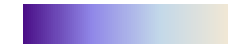
Σ = TRIG,  -Graphics-

σ0 = -130 °

Contours are {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18} (in degrees)

-Graphics3D-

## Choosing the wallpaper to go through minimizers.

#### PrimeθσϕMinimizer[Tmat, Σ] is the Σ-minimizer that will appear at the front corner of the wallpaper. If Tmat has more than one closest Σ-map, then θσϕMinimizers[Tmat, Σ] will not have all the Σ-minimizers.

```mathematica
Clear[PrimeθσϕMinimizer];
θσϕMinimizers[Tmat_,Σ_]:=θσϕ0to2π[#]&/@LeftCoset[bbG[Σ],UT[Tmat,Σ]];
SortedθσϕMinimizers[Tmat_,Σ_]:=Sort[θσϕMinimizers[Tmat,Σ],#1[[1]]<#2[[1]]||(#1[[1]]==#2[[1]]&&#1[[2]]<#2[[2]])&];
SortedθσϕMinimizers[Tmat_,Σ_]:=Sort[θσϕMinimizers[Tmat,Σ],#1[[3]]<#2[[3]]||(#1[[3]]==#2[[3]]&&#1[[2]]<#2[[2]])&];  (* Use this if the linoleum is otherwise too high *) 
PrimeθσϕMinimizer[Tmat_,Σ_]:=SortedθσϕMinimizers[Tmat,Σ][[1]];
(*PrimeθσϕMinimizer[Tmat_,ORTH]:=SortedθσϕMinimizers[Tmat,Σ][[5]];*)
PrimeθσϕMinimizer[Tmat_,CUBE]:=SortedθσϕMinimizers[Tmat,Σ][[1]];
PrimeθσϕMinimizer[Tmat_,XISO]:=If[θσϕ[Tmat,XISO][[1]]≥π,{-π+θσϕ[Tmat,XISO][[1]],-π,π-θσϕ[Tmat,XISO][[3]]},
{θσϕ[Tmat,XISO][[1]],-π,θσϕ[Tmat,XISO][[3]]}];
PrimeθσϕMinimizer[Tmat_,MONO]:=If[θσϕ[Tmat,MONO][[1]]≥π,{-π+θσϕ[Tmat,MONO][[1]],-π,π-θσϕ[Tmat,MONO][[3]]},
{θσϕ[Tmat,MONO][[1]],-π,θσϕ[Tmat,MONO][[3]]}];
```

## MinimizationFacts[Tmat, Σ] is needed for much of what follows.

#### May have to go back to AA file, then Clear and rerun nminimize. Not sure what is going on here .

```mathematica
Clear[θ,σ,ϕ];
Tmat=TmatMar17;
Σ=TRIG;
nRuns=3;
MinimizationFacts[Tmat,Σ]
```

```mathematica
MatrixNote[Tmat]
MatrixForm[UT[Tmat,Σ]]
```

#### If the WallPaperThroughMinimizers plot (later) puts the corners in the wall at awkward spots, then use the list of SortedθσϕMinimizers to choose a better PrimeθσϕMinimizer . The PrimeθσϕMinimizer gives the corner of the wall. The list of course depends on Tmat and Σ.

```mathematica
Tmat=TmatMar17;
MatrixNote[Tmat]
Σ=TRIG
ColumnForm[PaddedForm[#,{5,2}]&/@Round[SortedθσϕMinimizers[Tmat,Σ]/Degree,.1]]
PaddedForm[Round[PrimeθσϕMinimizer[Tmat,Σ]/Degree,.1],{5,2}]
```

```mathematica
Print[MatrixNote[Tmat],", ",Σ];
MatrixForm/@Round[LeftCoset[bbG[Σ],UT[Tmat,Σ]],.001]
```

```mathematica
θσϕMinimizersMiddleWall[Tmat_,Σ_]:=Select[θσϕMinimizers[Tmat,Σ],
#1[[1]]==PrimeθσϕMinimizer[Tmat,Σ][[1]]&&Abs[#[[2]]]<=Abs[PrimeθσϕMinimizer[Tmat,Σ][[2]]]&];
θσϕMinimizersMiddleWall[Tmat_,XISO]={};
```

```mathematica
GlideRot[{θ_,σ_,ϕ_}]:={θ+π,-σ,π-ϕ};
```

```mathematica
PointColor[Σ_]:=Black;
PointColor[TRIG]=Red;
PointColor[TET]=Green;
PointColor[ORTH]=Yellow;
PointColor[XISO]=Red;
PointColor[CUBE]=Hue[.5];
PointColor[CUBE]=Green;
PointColor[MONO]=Hue[.45];
```

#### WallPaperThroughMinimizers and LinoleumThroughMinimizers need to go inside Graphics3D.

```mathematica
θforMin[Tmat_,Σ_]:=PrimeθσϕMinimizer[Tmat,Σ][[1]];
σforMin[Tmat_,Σ_]:=PrimeθσϕMinimizer[Tmat,Σ][[2]];
```

```mathematica
WallPaperThroughMinimizers[Tmat_,Tmat00_,Σ_,ptsz_,plotpoints_,contourstyle_,eye_]:=
{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
WallPaper[Tmat,Tmat00,Σ,θforMin[Tmat,Σ],σforMin[Tmat,Σ],plotpoints,contourstyle],
{Thickness[.006],PointSize[ptsz],PointColor[Σ],
If[MemberQ[{XISO,MONO},Σ],
Line[{PrimeθσϕMinimizer[Tmat,Σ],PrimeθσϕMinimizer[Tmat,Σ]+{0,2π,0}}],
Point[MapEyeward[#,.06,eye]]&/@θσϕMinimizersMiddleWall[Tmat,Σ]],
If[MemberQ[{XISO,MONO},Σ],{},Point[MapEyeward[GlideRot[PrimeθσϕMinimizer[Tmat,Σ]],.15,eye]]]},  (* I will custom add this as a disk *)
If[WantBBC=="WantBBC",Text[Style["ℂ",1.35style],{π,1.12π,1.12π}]],
TicksForθσϕ};
```

```mathematica
LinoleumThroughMinimizers[Tmat_,Tmat00_,Σ_,plotpoints_,contourstyle_,eye_]:=
{{FaceForm[],EdgeForm[Thickness[.0015]],
Cuboid[{0,-π,0},{2π,π,0}],  (* base *)
Cuboid[{0,-π,0},{0,π,π}],
Cuboid[{0,π,0},{2π,π,π}],
Cuboid[{0,-π,PrimeθσϕMinimizer[Tmat,Σ][[3]]},{2π,π,PrimeθσϕMinimizer[Tmat,Σ][[3]]}]},  (* plane of linoleum *)
Line[{{2π,-π,0},{2π,-π,PrimeθσϕMinimizer[Tmat,Σ][[3]]}}],
cpΣFixϕ[Tmat,Tmat00,Σ,PrimeθσϕMinimizer[Tmat,Σ][[3]],plotpoints,contourstyle],
{Thickness[.007],PointSize[ptsz],PointColor[Σ],
If[MemberQ[{XISO,MONO},Σ],
Line[{PrimeθσϕMinimizer[Tmat,Σ],PrimeθσϕMinimizer[Tmat,Σ]+{0,2π,0}}],
{EdgeForm[],Polygon[Table[MapEyeward[#,.05,eye]+ZRot[t].{.08,0,0},{t,0,2π,.05π}]]}&/@Select[θσϕMinimizers[Tmat,Σ],
#1[[1]]==PrimeθσϕMinimizer[Tmat,Σ][[1]]&]]},
If[WantBBC=="WantBBC",Text[Style["ℂ",1.1style],{π,1.12π,1.12π}]],
TicksForθσϕ}
```

#### Text

```mathematica
TextForWallPaperThroughMinimizers[Tmat_,Tmat00_,Σ_,plotpoints_,contourstyle_,eye_]:=(
Print[MatrixNote[Tmat]];
Print[MatrixNote[Tmat00]];
Print["Σ = ",Σ,",  ",ColorData[colorscheme[Σ],"Panel"]];
Print["Front wall corner is (θ0, σ0) = (",DegreeText[θforMin[Tmat,Σ]],", ",DegreeText[σforMin[Tmat,Σ]],")"];
Print["The prime minimizer is at       (",DegreeText[θforMin[Tmat,Σ]],", ",DegreeText[σforMin[Tmat,Σ]],", ",DegreeText[PrimeθσϕMinimizer[Tmat,Σ][[3]]],"),   ",SubscriptBox[Style["β",13],Σ]//DisplayForm," = ",DegreeText[βT[Tmat,Σ]],"   ",ColorData[colorscheme[Σ]][(βT[Tmat,Σ]/Degree)/MaxForScaling[Tmat00,Σ]]];
Print["Contours of ",SubscriptBox["α",Σ]//DisplayForm," in the wallpaper are ",PrintNumeral[#,Tmat,Σ]&/@contours[Tmat00,Σ]," (in degrees)"];
Print["plotpoints = ",plotpoints];
PrintEye;)
```

```mathematica
TextForLinoleumThroughMinimizers[Tmat_,Tmat00_,Σ_,plotpoints_,contourstyle_,eye_]:=(
Print[MatrixNote[Tmat]];
Print["Σ = ",Σ,",  ",ColorData[colorscheme[Σ],"Panel"]];
Print["The prime minimizer is at (",DegreeText[PrimeθσϕMinimizer[Tmat,Σ][[1]]],", ",
                                                                                 DegreeText[PrimeθσϕMinimizer[Tmat,Σ][[2]]],", ",
                                                                                 DegreeText[PrimeθσϕMinimizer[Tmat,Σ][[3]]],"),   ",SubscriptBox[Style["β",13],Σ]//DisplayForm," = ",DegreeText[βT[Tmat,Σ]],"   ",ColorData[colorscheme[Σ]][(βT[Tmat,Σ]/Degree)/MaxForScaling[Tmat,Σ]]];
Print["Contours of ",SubscriptBox["α",Σ]//DisplayForm," in the linoleum are ",PrintNumeral[#,Tmat,Σ]&/@contours[Tmat00,Σ]," (in degrees)"];
Print["plotpoints = ",plotpoints];
PrintEye;)
```

#### The red contour value in the contour list is the smallest that has a non-empty contour in the diagram. It should be consistent with the legend.

```mathematica
Σ=TRIG;
imagesize=500;
style:=16 imagesize/500;
TforSuper=Style[" T ",.6style];
Tmat=TmatMar17;
Tmat00=Tmat;
WantBBC="NoWantBBC";
WantBeta="WantBeta";
WantPi="WantPi";
ptsz=.011;
eye=50xyzTP[{-50Degree,70Degree}];
contourstyle=Thickness[.0025];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

```mathematica
Σ=TRIG;
WantBBC="WantBBC";
WantBeta="WantBeta";
WantPi="WantPi";
ptsz=.011;
eye=50xyzTP[{-50Degree,70Degree}];
contourstyle=Thickness[.0025];
TextForLinoleumThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{LinoleumThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

#### DO NOT CHANGE definitions of θσϕ00, θσϕ11, θσϕ22. They are used later. Need PrimeθσϕMinimizer before running. And for that you need MinimizationFacts. (They both should have been run above.)

```mathematica
PrimeθσϕMinimizer[TmatMar17,TRIG]
```

```mathematica
Σ=TRIG;
θσϕTT={2π+50Degree,140Degree,0};   (* for Tmat *)
θσϕ00=PrimeθσϕMinimizer[TmatMar17,Σ];
θσϕ11={(104+1/2)Degree,50Degree,PrimeθσϕMinimizer[TmatMar17,Σ][[3]]};
θσϕ22={230Degree,120Degree,PrimeθσϕMinimizer[TmatMar17,Σ][[3]]};
Print[MatrixNote[TmatMar17]];
Print["θσϕ00 = ",θσϕ00];
Print["θσϕ11 = ",θσϕ11];
Print["θσϕ22 = ",θσϕ22];
Print["Σ = ",Σ];
Print["α_Σ^T(U_0) = ",Round[AlphaOfU[TmatMar17,UsHat[θσϕ00],Σ]/Degree,.1]];
Print["α_Σ^T(U_1) = ",Round[AlphaOfU[TmatMar17,UsHat[θσϕ11],Σ]/Degree,.1]];
Print["α_Σ^T(U_2) = ",Round[AlphaOfU[TmatMar17,UsHat[θσϕ22],Σ]/Degree,.1]];
```

#### θσϕ11 and θσϕ22 are both in the same horizontal plane as PrimeθσϕMinimizer[TmatMar17, TRIG]

```mathematica
ColumnForm[PaddedForm[#,{5,2}]&/@(SortedθσϕMinimizers[TmatMar17,TRIG]/Degree)]
PrimeθσϕMinimizer[TmatMar17,TRIG]/Degree
θσϕ11/Degree
θσϕ22/Degree
```

## Poster Fig. 8. Projections of TmatMar17 to three TRIG-subspaces. With T and linoleum.

#### The pdf file name is SI_AlphaTRIGlinoleumTwoTRIGsubspacesMar17.

```mathematica
zzrot=id;
zzrot=ZRot[-π/2];
```

```mathematica
RotBack[T_]:=MatrixUbar[zzrot].T.Transpose[MatrixUbar[zzrot]];
Print["zzrot = ",MatrixForm[zzrot]];
```

### Projections of TmatMar17 to the TRIG-subspaces.

```mathematica
Tmat=TmatMar17;
Tmat00=Tmat;
MatrixNote[Tmat]
MatrixNote[Tmat00]
Σ=TRIG;
imagesize=1200;
imagesize=700;
style:=16 imagesize/700;
AngRadDisk=3Degree;
ShiftToEye=.1 ;
ValuesOffset=1.2;
Δy=2.7;
TforSuper=Style[" T ",.6style];
eye=50xyzTP[{-50Degree,70Degree}];
WantPi="WantPi";
WantBBC="NoWantBBC";
WantBeta="WantBeta";
zzrot=ZRot[-π/2];
Δθσϕ={0,0,120Degree};
Print["θσϕ11 = ",θσϕ11];
Print["θσϕ22 = ",θσϕ22];
Print["Σ = ",Σ];
Print["(θ, ϕ) of U_0k is ",Round[{Theta[UsHat[θσϕ00].{0,0,1}]/Degree,Phi[UsHat[θσϕ00].{0,0,1}]/Degree}],"  Do the yellow arrows look right?"];
Print["(θ, ϕ) of U_1k is ",Round[{Theta[UsHat[θσϕ11].{0,0,1}]/Degree,Phi[UsHat[θσϕ00].{0,0,1}]/Degree}]];
Print["(θ, ϕ) of U_2k is ",Round[{Theta[UsHat[θσϕ22].{0,0,1}]/Degree,Phi[UsHat[θσϕ00].{0,0,1}]/Degree}]];
Print["α_Σ^T(U_0) = ",Round[AlphaOfU[Tmat,UsHat[θσϕ00],Σ]/Degree,.1]];
Print["α_Σ^T(U_1) = ",Round[AlphaOfU[Tmat,UsHat[θσϕ11],Σ]/Degree,.1]];
Print["α_Σ^T(U_2) = ",Round[AlphaOfU[Tmat,UsHat[θσϕ22],Σ]/Degree,.1]];
Print["Eigenvalues of P_2 are ",Eigenvalues[ProjToVSigOfU[Tmat,UsHat[θσϕ22],Σ]]];
Print["plotpoints = ",plotpoints,", AngRadDisk = ",AngRadDisk,", ShiftToEye = ",ShiftToEye];
Print["Contours of α_MONO on the spheres are ",PrintNumeral[#,Tmat,MONO]&/@contours[Tmat00,MONO]," (in degrees), but the red only applies to T"];  (* not sure *)
PrintEye;
Print["zzrot = ",MatrixForm[zzrot]];
Show[{
cpMONO[θσϕTT+Δθσϕ, BBrad,RotBack[Tmat],                                                                        contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[θσϕ00+Δθσϕ, BBrad,RotBack[ProjToVSigOfU[Tmat,UsHat[θσϕ00],Σ]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[θσϕ11+Δθσϕ, BBrad,RotBack[ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[θσϕ22+Δθσϕ, BBrad,RotBack[ProjToVSigOfU[Tmat,UsHat[θσϕ22],Σ]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
Graphics3D[{LinoleumThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,Thickness[0.002],eye],
{PointSize[.0001],Point/@{{250Degree,90Degree,PrimeθσϕMinimizer[Tmat,Σ][[3]]}}},
{Thickness[.00151],Line[{{2π,-π,0},{2π+π/2,-π,0},{2π+π/2,π,0},{2π,π,0}}]}, (* extension of base *)
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ00],θσϕ00+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
If[False,{         (* for checking yellow arrows *)
Paxes[True,True,True,ZRot[-π/2],θσϕ00+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],  Paxes[True,True,True,ZRot[-π/2],θσϕ11+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[True,True,True,ZRot[-π/2],θσϕ22+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[True,True,True,ZRot[-π/2],{3π,0,0},1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor]},{}],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ00],θσϕ00+Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
{Thickness[.005],                        (* spokes *)
Line[{θσϕTT,θσϕTT+Δθσϕ-{0,0,BBrad}}],  (* for Tmat *)
Line[{θσϕ00,θσϕ00+Δθσϕ-{0,0,BBrad}}],  (* at p0 *)
Line[{θσϕ11,θσϕ11+Δθσϕ-{0,0,BBrad}}], (* at p1 *)
Line[{θσϕ22,θσϕ22+Δθσϕ-{0,0,BBrad}}]}, (* at p2 *)
{Thickness[.001],Line[{θσϕ00,θσϕ00+0.98(cosd[140]UnitRight+sind[140]UnitUp)}]},
Text[Style["(θ_0, σ_0, ϕ_0)",.88style],                      θσϕ00+1.12(cosd[132]UnitRight+sind[132]UnitUp)],
{Thickness[.001],Line[{θσϕ11,θσϕ11+1.23(cosd[140]UnitRight+sind[140]UnitUp)}]},
Text[Style["(θ_1, σ_1, ϕ_1)",.88style],                      θσϕ11+1.40(cosd[136]UnitRight+sind[136]UnitUp)],
{Thickness[.001],Line[{θσϕ22,θσϕ22+0.83(cosd[35]UnitRight+sind[35]UnitUp)}]},
Text[Style["(θ_2, σ_2, ϕ_2)",.88style],                      θσϕ22+1.10(cosd[38]UnitRight+sind[38]UnitUp)],
Text[SubscriptBox[Style["P",Bold,style,SingleLetterItalics->False],Style["0",.7style]]//DisplayForm,θσϕ00+Δθσϕ+1.3BBrad(cosd[35]UnitRight+sind[35]UnitUp)],
Text[SubscriptBox[Style["P",Bold,style,SingleLetterItalics->False],Style["1",.7style]]//DisplayForm,θσϕ11+Δθσϕ+1.3BBrad(cosd[35]UnitRight+sind[35]UnitUp)],
Text[SubscriptBox[Style["P",Bold,style,SingleLetterItalics->False],Style["2",.7style]]//DisplayForm,θσϕ22+Δθσϕ+1.3BBrad(cosd[5]UnitRight+sind[5]UnitUp)],
Text[Style["T",Bold,style],θσϕTT+.95UnitRight+UnitUp],
Inset[Graphics[{
HorizontalLegends[Tmat,Σ,       contours[Tmat,Σ],      MaxForScaling[Tmat,Σ],      increment,ValuesOffset,Δy,TforSuper],
HorizontalLegends[Tmat,MONO,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],increment,ValuesOffset,-Δy,""]},ImageSize->250/700 imagesize],{π,0,-1.π}]
}]},ViewPoint->eye,Lighting->{{"Ambient",White}},BoxRatios->Automatic,Boxed->False,ImageSize->imagesize]
```

#### Be careful. T is not Mar17 but rather ProjToVSigOfU[etc]

```mathematica
Tmat=TmatMar17;
Σ=TRIG
nRuns=3;
MatrixNote[Tmat]
MinimizationFacts[ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ],Σ]
```

```mathematica
MatrixForm[UT[ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ],Σ]]
```

```mathematica
Σ
MatrixForm[UT[ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ],Σ]-UsHat[θσϕ11]]
```

```mathematica
Σ
MatrixForm[Chop[Transpose[MatrixUbar[UsHat[θσϕ11]]].ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ].MatrixUbar[UsHat[θσϕ11]],10^-5]]
MatrixForm[Round[%,1]]
```

#### UsHat[θσϕ22] and UT[ProjToVSigOfU[Tmat, UsHat[θσϕ22], Σ ], Σ] are in the same TRIG coset: CHECK THIS

```mathematica
Σ=TRIG;
MatrixForm[UsHat[θσϕ22]]
MatrixForm[UT[ProjToVSigOfU[Tmat,UsHat[θσϕ22],Σ],Σ]]
RotationAngle[UsHat[θσϕ22].Transpose[UT[ProjToVSigOfU[Tmat,UsHat[θσϕ22],Σ],Σ]]]/Degree
```

```mathematica
Overscript["U",RawBoxes["~"]]
Overscript["U",Style[RawBoxes["~"],16]]
```

#### To make sure MaxForScaling[Tmat, Σ] covers QQ, RR, and the projection. Where does this go? Do for the right maps.

#### RefMatQQ is a TRIG reference matrix for P(Tmat, 𝒱_TRIG(U)). See MinimizationFacts above.

```mathematica
RefMatQQ=Round[({{373.8927264509554, 0, -18.48152031801044, 0, 0, 0}, {0, 373.8927267149372, 0, -18.481519794732776, -1.6261736632827706*^-6, 0}, {-18.481520318010467, 0, 300.6227859324961, 0, 0, 0}, {0, -18.481519794732733, 0, 300.6227856685143, 0, 0}, {0, -1.626173613544779*^-6, 0, 0, 110.96897523309457, 22.743522188944542}, {0, 0, 0, 0, 22.74352218894454, 74.00000000000011}}),.01];
MatrixForm[RefMatQQ]
```

```mathematica
RefMatRR=({{374, 0, -100, 0, 0, 0}, {0, 374, 0, -100, 0, 0}, {-100, 0, 301, 0, 0, 0}, {0, -100, 0, 301, 0, 0}, {0, 0, 0, 0, 111, 23}, {0, 0, 0, 0, 23, 74}});
RefMatRR=({{374, 0, -18, 0, 0, 0}, {0, 374, 0, -18, 0, 0}, {-18, 0, 301, 0, 0, 0}, {0, -18, 0, 301, 0, 0}, {0, 0, 0, 0, 111, 23}, {0, 0, 0, 0, 23, 74}});
RefMatRR=({{374, 0, 100, 0, 0, 0}, {0, 374, 0, 100, 0, 0}, {100, 0, 301, 0, 0, 0}, {0, 100, 0, 301, 0, 0}, {0, 0, 0, 0, 111, 23}, {0, 0, 0, 0, 23, 74}});  (* changed -100 to 100 2025-03-08 *)
1.Eigenvalues[%]
```

#### RefMatSS is actually cubic .

```mathematica
MatrixForm[√6 verticalViaXAxis[{1,1,1}]]
```

```mathematica
RefMatSS=3TildeUofT[verticalViaXAxis[{1,1,1}],DiagonalMatrix[{1,1,1,2,2,3}]];
MatrixForm[RefMatSS]
```

```mathematica
MatrixForm[RefMatRR]
MatrixForm[TildeUofT[ZRot[π/3],RefMatRR]]
```

## Poster Fig 4. Two TRIG subspaces. No coordinate block.

```mathematica
U77=Simplify[ROT[46Degree,{-Cos[20 °], Sin[20 °],0}]];  (* not the same as UsHat[{70^∘, 0, 46^∘}] *)Simplify[Cross[{0,0,1},xyzTP[{70Degree,46Degree}]]/Cos[44 °]=={-Cos[20 °], Sin[20 °],0}]
Simplify[U77.{-Cos[20 °], Sin[20 °],0}=={-Cos[20 °], Sin[20 °],0}]
FullSimplify[RotationAngle[U77]==46Degree]
```

#### Note no RotBack here. The major inputs are RefMatQQ, RefMatRR, RefMatSS, and U77

```mathematica
Tmat=TmatMar17;  (* only needed for the Σ-subspace *)
Tmat00=Tmat;   (* only needed for the Σ-subspace *)
Σ=TRIG;
U77=UsHat[{70Degree,0,40Degree}];  (* custom for this figure only *)
U77=UswapVandKnoQualify[xyzTP[{70Degree,40Degree}]];
U77=Simplify[ROT[46Degree,Unit[Cross[{0,0,1},xyzTP[{70Degree,46Degree}]]]]];  (* not the same as UsHat[{70^∘, 0, 46^∘}] *)
U77=Simplify[ROT[46Degree,{-Cos[20 °], Sin[20 °],0}]];  (* not the same as UsHat[{70^∘, 0, 46^∘}] *)
eye=50xyzTP[{20Degree,60Degree}];
(*eye=50xyzTP[{-90Degree,90Degree}];*)
imagesize=600;imagesize=750;
style:=17 imagesize/800;
increment=2;
BBrad=1;
ArrowScale=.3;
ptsz=.01;
tkns=.002;
AngRadDisk=4Degree;
ShiftToEye=.2;
ValuesOffset=.8;
plotpoints=20;plotpoints=20;
Δy=1.;   (* Does not seem to do anything. Has to do with the inset, I think. Δy appears twice in the HorizontalLegends definition in AA. If you change one of them to, say, 2Δy, then you get some change. *)
WantBeta="NoWantBeta";
offset={0,0,.7};
centerQ={0,0,0};   
centerR=.9 3UnitUp;
centerS=.9 6UnitUp;
centerQpp=centerQ+3UnitRight;
centerRpp=centerR+3UnitRight;
centerSpp=centerS+3UnitRight;
WantLegendTest="NoWantLegendTest";
WantText="WantText";
Print["Contours for α_MONO on the spheres are ",contours[Tmat00,MONO]];
Print["plotpoints = ",plotpoints,", AngRadDisk = ",AngRadDisk,", ShiftToEye = ",ShiftToEye];
Print["U77 = ",MatrixForm[U77]];
PrintEye;
Show[{
cpMONO[centerQ, BBrad,1.RefMatQQ,contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],cpMONO[centerR, BBrad,1.RefMatRR,contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[centerS, BBrad,1.RefMatSS,contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[centerQpp, BBrad,1.MatrixUbar[U77].RefMatQQ.Transpose[MatrixUbar[U77]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[centerRpp, BBrad,1.MatrixUbar[U77].RefMatRR.Transpose[MatrixUbar[U77]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
cpMONO[centerSpp, BBrad,1.MatrixUbar[U77].RefMatSS.Transpose[MatrixUbar[U77]],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,Thickness[0.0015]],
Graphics3D[{
{FaceForm[GrayLevel[1]],EdgeForm[],Polygon/@Map[#+-3UnitRight&,SpherePolyList[1,0,360,0,180,15,15],{2}]}, (* plain sphere for id *)
Table[VisibleCurve[xyztp[{#,ϕ}]-3UnitRight&/@Range[0,360,3],1,eye,.0005,Black],{ϕ,15,165,15}],
Table[VisibleCurve[xyztp[{θ,#}]-3UnitRight&/@Range[0,180,3],1,eye,.0005,Black],{θ,0,345,15}],
{Thickness[.0005],Line[#-3UnitRight&/@PreCelSphereList[eye]]},
{FaceForm[GrayLevel[1]],EdgeForm[],Polygon/@Map[U77.#+6UnitRight&,SpherePolyList[1,0,360,0,180,15,15],{2}]}, (* plain sphere for U77 *)
Table[VisibleCurve[U77.xyztp[{#,ϕ}]+6UnitRight&/@Range[0,360,3],1,eye,.0005,Black],{ϕ,15,165,15}],
Table[VisibleCurve[U77.xyztp[{θ,#}]+6UnitRight&/@Range[0,180,3],1,eye,.0005,Black],{θ,0,345,15}],
{Thickness[.0005],Line[#+6UnitRight&/@PreCelSphereList[eye]]},

Paxes[False,False,True,id,-3UnitRight,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,id,centerQ,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,id,centerR,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,id,centerS,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],

Paxes[False,False,True,U77,+6UnitRight,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,U77,centerQpp,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,U77,centerRpp,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,U77,centerSpp,1.9,BBrad,ArrowScale,.004,"TriColor",ArrowColor],

TwoFoldGraphics[TRIG,id,-3UnitRight,1,1.2AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,id,centerQ,1,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,id,centerR,1,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,id,centerS,1,AngRadDisk,ShiftToEye,eye,tkns,Green],

TwoFoldGraphics[TRIG,U77,+6UnitRight,1,1.2AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,U77,centerQpp,1,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,U77,centerRpp,1,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[TRIG,U77,centerSpp,1,AngRadDisk,ShiftToEye,eye,tkns,Green],
Text[Style["Q",1.02style,SingleLetterItalics->False],centerQ+1.3(cosd[220]UnitRight+sind[220]UnitUp)],
Text[Style["R",1.02style,SingleLetterItalics->False],centerR+1.3(cosd[220]UnitRight+sind[220]UnitUp)],
Text[Style["S",1.02style,SingleLetterItalics->False],centerS+1.3(cosd[220]UnitRight+sind[220]UnitUp)],
Text[SequenceForm[Overscript[Style["U",1.02style,Italic],Style[RawBoxes["~"],1.8style]],Style["(",1.02style],Style["Q",1.02style,SingleLetterItalics->False],Style[")",1.02style]],centerQpp+1.45(cosd[-40]UnitRight+sind[-40]UnitUp)],
Text[SequenceForm[Overscript[Style["U",1.02style,Italic],Style[RawBoxes["~"],1.8style]],Style["(",1.02style],Style["R",1.02style,SingleLetterItalics->False],Style[")",1.02style]],centerRpp+1.45(cosd[-40]UnitRight+sind[-40]UnitUp)],
Text[SequenceForm[Overscript[Style["U",1.02style,Italic],Style[RawBoxes["~"],1.8style]],Style["(",1.02style],Style["S",1.02style,SingleLetterItalics->False],Style[")",1.02style]],centerSpp+1.45(cosd[-40]UnitRight+sind[-40]UnitUp)],
(*HERE *)Text[SequenceForm[SubscriptBox[Style["ℤ",style],Style["2",.6style]]//DisplayForm,Style["(",style],SubscriptBox[Style["𝕌",style],Style["TRIG",.55style]]//DisplayForm,Style[")",style]],-3UnitRight-1.4UnitUp],
Text[SequenceForm[Style["U ",style],Style["  ",.3style],SubscriptBox[Style["ℤ",style],Style["2",.6style]]//DisplayForm,Style["(",style],SubscriptBox[Style["𝕌",style],Style["TRIG",.55style]]//DisplayForm,Style[")",style]],+6UnitRight-1.4UnitUp],Text[SequenceForm[SubscriptBox[Style["𝒱",1.05style],Style["TRIG",.55style]]//DisplayForm,Style["(I )",style]],centerQ-1.4UnitUp],
Text[SequenceForm[SubscriptBox[Style["𝒱",1.05style],Style["TRIG",.55style]]//DisplayForm,Style["(U )",style]],centerQ+3UnitRight-1.4UnitUp],
Inset[Graphics[
HorizontalLegends[Tmat,MONO,contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],increment,ValuesOffset,Δy,""],ImageSize->200/700 imagesize],1.83UnitRight+7.5UnitUp]}]},ImageSize->imagesize,Boxed->False,ViewPoint->eye, Lighting->{{"Ambient",White}}]
```

## Poster Fig 7. Two TRIG-subspaces with a few members. No linoleum. No Tmat except to determine contours. RefMatQQ, RefMatRR, RefMatSS are the same as in Poster Fig 4.

#### The pdf file name is SI_AlphaNOlinoleumTwoTRIGsubspacesMar17, in moment_tensor_tex folder.

```mathematica
Tmat=TmatMar17;
eye=50xyzTP[{-50Degree,70Degree}];
Σ=TRIG;  (* Σ determines the subspace for the projection P, but the contours are contours of Subscript[α, MONO], whatever the elastic map *)
imagesize=1200;
imagesize=700;
style:=16 imagesize/700;
AngRadDisk=3Degree;
plotpoints=20;
zzrot=ZRot[-π/2];
TforSuper=Style[" ",.6style,Bold]; (* for superscript *)
ValuesOffset=.7;
WantPi="NoWantPi";
WantBBC="NoWantBBC";
WantBeta="NoWantBeta";
(*PP=ProjToVSigOfU[Tmat,UsHat[θσϕ11],Σ];*)
Δθσϕ={0,0,120Degree};
Print["θσϕ11 = ",θσϕ11];
Print["θσϕ22 = ",θσϕ22];
Print["RefMatQQ = ",MatrixForm[RefMatQQ]];  (* RefMatQQ was changed 2025-03-08 *)
Print["RefMatRR = ",MatrixForm[RefMatRR]];  
Print["RefMatSS = ",MatrixForm[RefMatSS]];  
Print["(θ, ϕ) of U_1k is ",Round[{Theta[UsHat[θσϕ11].{0,0,1}]/Degree,Phi[UsHat[θσϕ00].{0,0,1}]/Degree}],"  Do the yellow arrows look right?"];
Print["(θ, ϕ) of U_2k is ",Round[{Theta[UsHat[θσϕ22].{0,0,1}]/Degree,Phi[UsHat[θσϕ00].{0,0,1}]/Degree}],"  Do the yellow arrows look right?"];
Print["plotpoints = ",plotpoints,", AngRadDisk = ",AngRadDisk,", ShiftToEye = ",ShiftToEye];
Print["Contours for α_MONO on the spheres are ",contours[Tmat,MONO]];
Print["zzrot = ",MatrixForm[zzrot]];
PrintEye;
Show[{If[True,{
cpMONO[θσϕ11+Δθσϕ,         BBrad,RotBack[TildeUofT[UsHat[θσϕ11],RefMatQQ]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]],
cpMONO[θσϕ11+2.3Δθσϕ, BBrad,RotBack[TildeUofT[UsHat[θσϕ11],RefMatRR]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]],
cpMONO[θσϕ11+3.6Δθσϕ, BBrad,RotBack[TildeUofT[UsHat[θσϕ11],RefMatSS]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]],

cpMONO[θσϕ22+Δθσϕ,         BBrad,RotBack[TildeUofT[UsHat[θσϕ22],RefMatQQ]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]], (* W̃(P) on θσϕ22 spoke *)
cpMONO[θσϕ22+2.3Δθσϕ, BBrad,RotBack[TildeUofT[UsHat[θσϕ22],RefMatRR]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]], (* W̃(Q) on θσϕ22 spoke *)
cpMONO[θσϕ22+3.6Δθσϕ, BBrad,RotBack[TildeUofT[UsHat[θσϕ22],RefMatSS]],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]]},{}],(* W̃(R) on θσϕ22 spoke *)

Graphics3D[{{PointSize[.0001],Point/@{{250Degree,90Degree,PrimeθσϕMinimizer[Tmat,Σ][[3]]}}},
{FaceForm[],EdgeForm[Thickness[.0015]],Thickness[.0015],
Cuboid[{0,-π,0},{2π,π,0}],  (* base *)
Line[{{0,π,0},{0,-π,0},{0,-π,π},{0,π,π}}], (* left face *)
Line[{{0,π,PrimeθσϕMinimizer[Tmat,Σ][[3]]},{0,π,π},{2π,π,π},{2π,π,0},{0,π,0}}]},   (* right rear face *)
{GrayLevel[.7],Polygon[{
{0,    -π,.99PrimeθσϕMinimizer[Tmat,Σ][[3]]},
{2π,-π,.99PrimeθσϕMinimizer[Tmat,Σ][[3]]},
{2π,   π,.99PrimeθσϕMinimizer[Tmat,Σ][[3]]},
{0,      π,.99PrimeθσϕMinimizer[Tmat,Σ][[3]]}}]}, (* plane of linoleum *)
{Thickness[.00151],
Line[{{θσϕ11[[1]],-π,0},{θσϕ11[[1]],-π,θσϕ11[[3]]},{θσϕ11[[1]],π,θσϕ11[[3]]}}],
Line[{{θσϕ22[[1]],-π,0},{θσϕ22[[1]],-π,θσϕ22[[3]]},{θσϕ22[[1]],π,θσϕ22[[3]]}}],(* horizontal lines through p1 and p2 *)
Line[{{2π,-π,0},{2π,-π,θσϕ22[[3]]}}]}, 
If[False,{         (* for checking yellow arrows *)
Paxes[True,True,True,ZRot[-π/2],θσϕ11+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[True,True,True,ZRot[-π/2],θσϕ22+Δθσϕ,1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[True,True,True,ZRot[-π/2],{3π,0,0},1.8,BBrad,ArrowScale,.004,"TriColor",ArrowColor]},{}],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+       Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+2.3Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+3.6Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+       Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],(* on θσϕ22 spoke *)
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+2.3Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],(* on θσϕ22 spoke *)
Paxes[False,False,True,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+3.6Δθσϕ,1.6,BBrad,ArrowScale,.004,"TriColor",ArrowColor],(* on θσϕ22 spoke *)
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+       Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+2.3Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ11],θσϕ11+3.6Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+       Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],     (* on θσϕ22 spoke *)
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+2.3Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],     (* on θσϕ22 spoke *)
TwoFoldGraphics[Σ,ZRot[-π/2].UsHat[θσϕ22],θσϕ22+3.6Δθσϕ,BBrad,AngRadDisk,ShiftToEye,eye,tkns,Green],     (* on θσϕ22 spoke *)
{Thickness[.004],                        (* spokes *)

Line[{θσϕ11,θσϕ11+Δθσϕ-{0,0,BBrad}}], (* spoke at θσϕ11 *)
{If[True,Black,Red],Line[{θσϕ11+Δθσϕ+{0,0,BBrad},θσϕ11+2.3Δθσϕ-{0,0,BBrad}}]},(* spoke at θσϕ11 *)
Line[{θσϕ11+2.3Δθσϕ+{0,0,BBrad},θσϕ11+3.6Δθσϕ-{0,0,BBrad}}], (* spoke at θσϕ11 *)

Line[{θσϕ22,θσϕ22+Δθσϕ-{0,0,BBrad}}], (* spoke at θσϕ22 *)
Line[{θσϕ22+Δθσϕ+{0,0,BBrad},θσϕ22+2.3Δθσϕ-{0,0,BBrad}}],  (* spoke at θσϕ22 *)
Line[{θσϕ22+2.3Δθσϕ+{0,0,BBrad},θσϕ22+3.6Δθσϕ-{0,0,BBrad}}]},  (* spoke at θσϕ22 *)

{Thickness[.002],                    Line[{θσϕ11,θσϕ11+1.27(cosd[140]UnitRight+sind[140]UnitUp)}]},
Text[Style["(θ_1, σ_1, ϕ_1)",style],θσϕ11+1.56(cosd[140]UnitRight+sind[140]UnitUp)],
{Thickness[.002],                    Line[{θσϕ22,θσϕ22+0.87(cosd[35]UnitRight+sind[35]UnitUp)}]},
Text[Style["(θ_2, σ_2, ϕ_2)",style],θσϕ22+1.21(cosd[35]UnitRight+sind[35]UnitUp)],

Text[SequenceForm[Overscript[Style["U_1",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["Q",style,Bold],Style[")",style]],θσϕ11+        Δθσϕ-1.42UnitRight],(* OverTilde[Subscript[U, 1]](Q) on θσϕ11 spoke *)    
Text[SequenceForm[Overscript[Style["U_1",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["R",style,Bold],Style[")",style]],θσϕ11+2.3Δθσϕ-1.42UnitRight], (* OverTilde[Subscript[U, 1]](R) on θσϕ11 spoke *)    
Text[SequenceForm[Overscript[Style["U_1",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["S",style,Bold],Style[")",style]],θσϕ11+3.6Δθσϕ-1.42UnitRight], (* OverTilde[Subscript[U, 1]](S) on θσϕ11 spoke *)    
  
Text[SequenceForm[Overscript[Style["U_2",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["Q",style,Bold],Style[")",style]],θσϕ22+       Δθσϕ+1.45UnitRight], (* OverTilde[Subscript[U, 2]](Q) on θσϕ22 spoke *)        
Text[SequenceForm[Overscript[Style["U_2",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["R",style,Bold],Style[")",style]],θσϕ22+2.3Δθσϕ+1.45UnitRight],(* OverTilde[Subscript[U, 2]](R) on θσϕ22 spoke *)
Text[SequenceForm[Overscript[Style["U_2",.98style],Style[RawBoxes["~"],1.8style]],Style["(",style],Style["S",style,Bold],Style[")",style]],θσϕ22+3.6Δθσϕ+1.45UnitRight],(* OverTilde[Subscript[U, 2]](S) on θσϕ22 spoke *)
Text[SequenceForm[SubscriptBox[Style["𝒱",1.2style],Style["TRIG",.6style]]//DisplayForm,Style["(U_1)",1.05style]],θσϕ11+3.6Δθσϕ+1.7UnitUp],
Text[SequenceForm[SubscriptBox[Style["𝒱",1.2style],Style["TRIG",.6style]]//DisplayForm,Style["(U_2)",1.05style]],θσϕ22+3.6Δθσϕ+1.95UnitUp],
TicksForθσϕ,
Inset[Graphics[{HorizontalLegends[Tmat,MONO,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],increment,ValuesOffset,Δy,TforSuper]},ImageSize->320/700 imagesize],{π,0,-.85π}]}]},Lighting->{{"Ambient",White}},ImageSize->imagesize,Boxed->False,ViewPoint->eye,BoxRatios->Automatic]
```

## Contour plots on the wall.

```mathematica
Σ=TET;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=550;
style:=14 imagesize/500;
ValuesOffset=.85;
Δy=0.;
WantBBC="WantBBC";  
WantBeta="WantBeta";
ptsz=.011;
contourstyle=Thickness[.0025];
eye=50xyzTP[{-50Degree,70Degree}];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

#### Need to think about the color coding here:

```mathematica
Σ=MONO;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=550;
style:=14 imagesize/500;
ValuesOffset=.85;
Δy=0.;
WantBBC="WantBBC"; 
WantBeta="WantBeta";
ptsz=.011;
contourstyle=Thickness[.0025];
eye=50xyzTP[{-50Degree,70Degree}];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

```mathematica
Σ=XISO;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=550;
style:=14 imagesize/500;
ValuesOffset=.85;
Δy=0.;
WantBBC="WantBBC";  
WantBeta="WantBeta";
ptsz=.011;
contourstyle=Thickness[.0025];
eye=50xyzTP[{-50Degree,70Degree}];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

```mathematica
Σ=ORTH;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=550;
style:=14 imagesize/500;
ValuesOffset=.85
Δy=0.;
WantBBC="WantBBC";  
WantBeta="WantBeta";
ptsz=.011;
eye=50xyzTP[{-50Degree,70Degree}];
contourstyle=Thickness[.0025];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

```mathematica
Tmat=TmatMar17;
MatrixNote[Tmat]
Σ=CUBE
ColumnForm[PaddedForm[#,{5,2}]&/@Round[SortedθσϕMinimizers[Tmat,Σ]/Degree,.1]]
PaddedForm[Round[PrimeθσϕMinimizer[Tmat,Σ]/Degree,.1],{5,2}]
```

```mathematica
Σ=CUBE;
Tmat=TmatMar17;
Tmat00=Tmat;
imagesize=550;
style:=14 imagesize/500;
ValuesOffset=1.1;
Δy=0.;
WantBBC="WantBBC";  
WantBeta="WantBeta";
ptsz=.011;
eye=50xyzTP[{-50Degree,70Degree}];
contourstyle=Thickness[.0025];
TextForWallPaperThroughMinimizers[Tmat,Tmat00,Σ,plotpoints,contourstyle,eye];
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,Σ,ptsz,plotpoints,contourstyle,eye],
Inset[Graphics[
HorizontalLegends[Tmat,Σ,contours[Tmat,Σ],MaxForScaling[Tmat,Σ],increment,ValuesOffset,Δy,TforSuper],ImageSize->350/700 imagesize],{π,0,-.9π}]},BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->imagesize,Lighting->{{"Ambient",White}}]
```

## α_MONO^T on the sphere and on the block.

#### RefMatMM is used in the figure for α_MONO^Ton the sphere and α_MONO^T on the block.

```mathematica
RefMatMM=({{350, 0, 50, 0, 0, 0}, {0, 350, 0, 50, 0, 0}, {50, 0, 200, 0, 0, 0}, {0, 50, 0, 200, 0, 0}, {0, 0, 0, 0, 111, 23}, {0, 0, 0, 0, 23, 74}});  
Eigenvalues[1.RefMatMM]
```

```mathematica
contours[RefMatMM,MONO]
```

```mathematica
plotpoints=5;
Show[cpMONO[{0,0,0}, BBrad,1.RefMatMM,contours[RefMatMM,MONO],MaxForScaling[RefMatMM,MONO],plotpoints,Thickness[0.0015]], Lighting->{{"Ambient",White}}]
```

#### v is a point on 𝕊^2. The specification of σ in PutOnWall puts it on the front or back wall appropriately.

```mathematica
PutOnWall[v_,Tmat_,U_,Σ_]:={Mod[Theta[U.v],2π],If[Mod[Theta[U.v],2π]>θforMin[Tmat,Σ],π,-π],Phi[U.v]}
```

```mathematica
DiskOnWall[center_,radius_,eye_]:=Table[MapEyeward[center,.1,eye]+YRot[t].{0,0,radius},{t,0,2π,.05π}];
```

```mathematica
U88=ZRot[70Degree].YRot[30Degree];
Tmat=1.MatrixUbar[U88].RefMatRR.Transpose[MatrixUbar[U88]];
Tmat=1.MatrixUbar[U88].RefMatMM.Transpose[MatrixUbar[U88]];
Print["Tmat = [OverBar[U88]]",MatrixForm[RefMatMM],"[OverBar[U88]]^T"];
Tmat00=Tmat;
Σ=MONO;
AngRadDisk=3Degree;
ShiftToEye=0.2;
eye=50xyzTP[{-50Degree,70Degree}];
BBrad0=1.7;
SphereCenter={3.5π,0,π/2};
imagesize=700;
imagesize=1200;
style:=12 imagesize/700;
plotpoints=20;
ArrowScale=.25;
TforSuper=Style[" T  ",.8style,Bold];  (* for superscript *)
increment=2;
zzrot=ZRot[-π/2];
WantBBC="WantBBC";
WantBeta="WantBeta";
WantPi="WantPi";
WantLegendTest="NoWantLegendTest";test=6;
ValuesOffset=.8;
ptsz=.01;
contourstyle=Thickness[.0015];
Print["plotpoints = ",plotpoints,", AngRadDisk = ",AngRadDisk,", ShiftToEye = ",ShiftToEye];
PrintEye;
Print["PrimeθσϕMinimizer = ",Round[PrimeθσϕMinimizer[Tmat,Σ]/Degree,.1]];
Print["RefMatMM = ",MatrixForm[RefMatMM]];
Print["U88 = ",MatrixForm[Simplify[U88]]];
Print["zzrot = ",MatrixForm[zzrot]];
Show[{
cpMONO[SphereCenter,BBrad0,RotBack[Tmat],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
Graphics3D[{WallPaperThroughMinimizers[Tmat,Tmat00,MONO,ptsz,plotpoints,contourstyle,eye], (* no RotBack since this is in ℂ *)TwoFoldGraphics[TRIG,zzrot.U88,SphereCenter,BBrad0,.8AngRadDisk,ShiftToEye,eye,tkns,Green],
Paxes[False,False,True,zzrot.U88,SphereCenter,1.6BBrad0,BBrad0,1.5ArrowScale,.004,"TriColor",ArrowColor],  (* the yellow arrow *)
Paxes[True,  True,  True,zzrot,          SphereCenter,1.5BBrad0,BBrad0,1.5ArrowScale,.004,"Gray",ArrowColor], (* the xyz axes *)
Text[Style["x",1.12style],SphereCenter+zzrot.{1.7BBrad0,0,0}],
Text[Style["y",1.12style],SphereCenter+zzrot.{0,1.65BBrad0,0}],
{EdgeForm[],Black,Polygon[DiskOnWall[{Theta[U88.{0,0,1}],       -π,       Phi[U88.{0,0,1}]},.08,eye]]}, (* 3-fold point on wall, no zzrot for stuff on wall *)
{EdgeForm[],Black,Polygon[DiskOnWall[{Theta[U88.{0,0,1}]+π,   π,π-Phi[U88.{0,0,1}]},.08,eye]]}, (* 3-fold point on wall, no zzrot for stuff on wall *)
ThreeFoldGraphics[TRIG,zzrot.U88,SphereCenter,BBrad0,AngRadDisk,ShiftToEye,eye,tkns,Black], (* 3-fold point on SPHERE *)
{EdgeForm[],Green,Polygon[DiskOnWall[#,.06,eye]]}&/@Table[PutOnWall[ZRot[n π/3].{0,1,0},Tmat,U88,Σ],{n,1,6}],
Inset[Graphics[HorizontalLegends[Tmat,MONO,contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],increment,ValuesOffset,Δy,TforSuper],ImageSize->.26imagesize],{π,0,-.9π}]}]},ViewPoint->eye,Lighting->{{"Ambient",White}},BoxRatios->Automatic,Boxed->False,ImageSize->imagesize]
```

## Poster Fig. 6. Diagram showing UsHat[{θ, σ, ϕ}] acting on the InitialSquare (a cube). The figure in the paper has UhatPicture above RightPicture. I do not know where that figure is.

```mathematica
ss=.1;
InitialSquare=cube[id,{0,0,1},ss,True];
AxesOnSquare={Line[{{-3ss,0,1},{-ss,0,1}}],Line[{{ss,0,1},{3ss,0,1}}],
                           Line[{{0,-3ss,1},{0,-ss,1}}],Line[{{0,ss,1},{0,3ss,1}}]};
```

```mathematica
InitialSquare[[1]]
InitialSquare[[1,1]]
InitialSquare[[1,2]]
InitialSquare[[1,2,1]]
InitialSquare[[1,2,1,4]]
```

```mathematica
UhatPicture[θ_,σ_,ϕ_,eye_]:=Graphics3D[{{GrayLevel[.8],Opacity[.7],Sphere[{0,0,0}]},
Paxes[True,True,False,id,{0,0,0},1.4,1,ArrowScale,.009,"Gray",ArrowColor],
Paxes[False,False,True,id,{0,0,1},.35,0,.7ArrowScale,.006,"TriColor",ArrowColor],
Paxes[False,False,True,UsHat[{θ,0,ϕ}],UsHat[{θ,0,ϕ}].{0,0,1},.35,0,.7ArrowScale,.006,"TriColor",ArrowColor],
Paxes[False,False,True,UsHat[{0,0,ϕ}],UsHat[{0,0,ϕ}].{0,0,1},.35,0,.7ArrowScale,.006,"TriColor",ArrowColor],,
VisibleCurve[EquatorList,1,eye,.002,Black],
VisibleCurve[XRot[π/2].#&/@EquatorList,1,eye,.002,Black],
VisibleCurve[ZRot[θ].XRot[π/2].#&/@EquatorList,1,eye,.002,Black],
{Thickness[.002],
Map[MapEyeward[#,.05,eye]&,AxesOnSquare,{3}],
Map[MapEyeward[#,.05,eye]&,Map[YRot[ϕ].#&,AxesOnSquare,{3}],{3}],
(*Map[MapEyeward[#,.05,eye]&,Map[ZRot[θ].YRot[ϕ].#&,AxesOnSquare,{3}],{3}],*)
Map[MapEyeward[#,.07,eye]&,Map[ZRot[θ].YRot[ϕ].ZRot[σ].#&,AxesOnSquare,{3}],{3}]},
Text[Style["θ",18],xyzTP[{θ/2,83Degree}]],
Text[Style["ϕ",18],xyzTP[{-18Degree,ϕ/2}]],
Text[SubscriptBox[Style["Û",18],Style["(0, 0, 0)",13]]//DisplayForm,1.25xyzTP[{-π/2,20Degree}]],
Text[SubscriptBox[Style["Û",18],Style["(0, 0, ϕ)",13]]//DisplayForm,UsHat[{0-50Degree,0,ϕ-5Degree}].{0,0,1}],
Text[SubscriptBox[Style["Û",18],If[σ==0,Style["(θ, 0, ϕ)",13],Style["(θ, σ, ϕ)",13]]]//DisplayForm,UsHat[{θ+50Degree,0,ϕ+0Degree}].{0,0,1}],
If[σ!=0,Text[Style["σ",18],ZRot[θ].YRot[ϕ].({0,0,1}+2.6ss(ZRot[σ/2].{-1,0,0}))]],
Text[Style["x",20],{1.55,0,0}],
Text[Style["y",20],{0,1.5,0}],
InitialSquare,
Map[YRot[ϕ].#&,InitialSquare,{4}],
Map[ZRot[θ].YRot[ϕ].ZRot[σ].#&,InitialSquare,{4}]},ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->400];
```

```mathematica
θ=70Degree;
ϕ=60Degree;
σ=0Degree;σ=70Degree;
eye=50xyzTP[{30Degree,70Degree}];
eye=50xyzTP[{-55Degree+90Degree,70Degree}];
ArrowScale=.15;
PrintEye;LeftPicture=GraphicsRow[{UhatPicture[θ,0,ϕ,eye],UhatPicture[θ,σ,ϕ,eye]},ImageSize->900]
```

```mathematica
WantBBC=="WantBBC"
```

```mathematica
θ=70Degree;
ϕ=60Degree;
σ=0Degree;σ=70Degree;
Σ=CUBE;
WantColor=True;
WantText="WantText";
WantBBC="WantBBC";
ArrowScale=.15;
scale=.3;
scale=.25;
eye=50xyzTP[{-55Degree,70Degree}];
U1=UsHat[{0Degree,0Degree,0Degree}];   
U2=YRot[ϕ].U1;
U3=ZRot[θ].U2;
U4=UsHat[{θ,σ,ϕ}];
Ulist={U1,U2,U3,U4};
Print["Σ = ",Σ];
PrintEye;
RightPicture=Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.0015],
Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[{U2}],  (* line segments front to back *)
Line[{{0,0,0},{0,0,ϕ},{θ,0,ϕ},{θ,π,ϕ}}],
Line[{{0,0,0},{θ,0,0},{θ,0,ϕ}}],
Line[{{θ,0,0},{θ,π,0},{θ,π,ϕ},{0,π,ϕ}}],
Line[{{2π,0,0},{2π,0,ϕ}}]},
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.0012],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[{U2}],
If[WantBBC=="WantBBC",Text[Style["ℂ",1.35style],{π,1.12π,1.12π}]];
shape[#,Σ,scale,WantColor]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
If[WantText=="WantText",{
If[WantBBC=="WantBBC",Text[Style["ℂ",24],{π,1.12π,1.11π}]],
Text[Style["I ",17,Italic],{2π,0,0}+{1.2,-1.3,0}],
Text[Style["I ",17,Italic],{0,   0,0}+{1.2,-1.3,0}]
(*Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.75}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.75}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.75}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.8}]*)}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->{{"Ambient",White}},ImageSize->650]
```

```mathematica
GraphicsRow[{LeftPicture,RightPicture},ImageSize->1100]
```

#### The old diagram

```mathematica
ss=.3;
InitialSquare={0,0,1}+ss √2 ZRot[# π/2].unit[{1,1,0}]&/@Range[4];
AxesOnSquare={Line[{{-ss,0,1},{ss,0,1}}],Line[{{0,-ss,1},{0,ss,1}}]};
```

```mathematica
θ=60Degree;
ϕ=60Degree;
σ=40Degree;
tt=.65;
eye=20xyzTP[{30Degree,70Degree}];
ArrowScale=.15;
PrintEye;
Graphics3D[{{GrayLevel[.8],Sphere[{0,0,0}]},
Paxes[True,True,True,id,{0,0,0},1.4,1,ArrowScale,.009,"Gray",ArrowColor],
{Thickness[.002],
Line[EquatorList],
Line[XRot[π/2].#&/@EquatorList],
Line[ZRot[θ].XRot[π/2].#&/@EquatorList]},
{EdgeForm[],FaceForm[Black],Polygon/@(DiskOnSphere[#.{0,0,1},.8AngRadDisk,20ShiftToEye,eye]&/@{id,YRot[ϕ],ZRot[θ].YRot[ϕ]})},
{Thickness[.002],
Map[MapEyeward[#,.05,eye]&,AxesOnSquare,{3}],
Map[MapEyeward[#,.05,eye]&,Map[YRot[ϕ].#&,AxesOnSquare,{3}],{3}],
Map[MapEyeward[#,.05,eye]&,Map[ZRot[θ].YRot[ϕ].#&,AxesOnSquare,{3}],{3}],
Map[MapEyeward[#,.07,eye]&,Map[ZRot[θ].YRot[ϕ].ZRot[σ].#&,AxesOnSquare,{3}],{3}]},
Text[Style["θ",18],xyzTP[{θ/2,83Degree}]],
Text[Style["ϕ",18],xyzTP[{-18Degree,ϕ/2}]],
Text[Style["σ",18],ZRot[θ].YRot[ϕ].({0,0,1}+.7ss(Cos[σ/2]{0,1,0}+Sin[σ/2]{-1,0,0}))],
Text[SubscriptBox[Style["Û",18],Style["(0, 0, 0)",13]]//DisplayForm,1.25xyzTP[{-π/2,20Degree}]],
Text[SubscriptBox[Style["Û",18],Style["(0, 0, ϕ)",13]]//DisplayForm,1.25xyzTP[{-65Degree,1.1ϕ}]],
Text[SubscriptBox[Style["Û",18],Style["(θ, 0, ϕ)",13]]//DisplayForm,UsHat[{θ,0,ϕ}].({0,0,1}+ss{-.75,1,0}+tt{0,1,0})],
Text[SubscriptBox[Style["Û",18],Style["(θ, σ, ϕ)",13]]//DisplayForm,UsHat[{θ,σ,ϕ}].({0,0,1}+ss{-.75,1,0}+.8tt{0,1,0})],
Text[Style["x",20],{1.8,0,0}],
Text[Style["y",20],{0,1.5,0}],
Line[UsHat[{θ,0,ϕ}].#&/@{{0,0,1}+ss{-.75,1,0},{0,0,1}+ss{-.75,1,0}+.55tt{0,1,0}}],
Line[UsHat[{θ,σ,ϕ}].#&/@{{0,0,1}+ss{-.75,1,0},{0,0,1}+ss{-.75,1,0}+.55tt{0,1,0}}],
{Orange,EdgeForm[Thickness[.002]],
Polygon[MapEyeward[#,.05,eye]&/@InitialSquare],
Polygon[MapEyeward[YRot[ϕ].#,.05,eye]&/@InitialSquare],
Polygon[MapEyeward[ZRot[θ].YRot[ϕ].#,.05,eye]&/@InitialSquare]},
{Opacity[.5],EdgeForm[Thickness[.002]],Polygon[MapEyeward[ZRot[θ].YRot[ϕ].ZRot[σ].#,.07,eye]&/@InitialSquare]}},ViewPoint->eye,Boxed->False,Lighting->"Neutral",ImageSize->500]
```

#### Orthorhombic example for the Pictures for Elastic Maps paper. Must run MinimizationFacts[Tmat, MONO] in order to get β.

```mathematica
UU=1.XRot[-15Degree].ZRot[-15Degree].YRot[10Degree];
Print["UU = ",MatrixForm[UU]," = ",MatrixForm[Round[UU,.001]]];
Tmat=1.TildeUofT[UU,({{2., 0, 0, 0, 0, 0}, {0, 6, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 4, 1, 0}, {0, 0, 0, 1, 1, 0}, {0, 0, 0, 0, 0, 3}})];
Simplify[Eigenvalues[Tmat]]
AlphaOfU[Tmat,UU,ORTH]
```

### note: you may need to enter Clear[nminimize] in common_funs.nb (You may also need to re-enter Tmat in the block above.)

```mathematica
nRuns=2;
MinimizationFacts[Tmat,MONO]
```

```mathematica
Σ=MONO;
WantBeta="NoWantBeta";
TforSuper="T";
increment=1;
style=15;
ArrowScale=.018;
contourstyle=Thickness[.002];
Print["UU = ",MatrixForm[UU]," = ",MatrixForm[Round[UU,.001]]];
Print["Tmat = ",MatrixForm[Chop[Tmat]]," = ",MatrixForm[Round[Tmat,.001]]];
Print["contours for Tmat  are ",contours[Tmat,MONO]];
Print["MaxForScaling[Tmat, MONO] = ",MaxForScaling[Tmat,MONO]];
eye=50xyzTP[{35Degree,65Degree}];
eye=50UU.{0,0,1.};
plotpoints=20;
ArrowScale=.18;
Print["plotpoints = ",plotpoints];
PrintEye;
Show[{cpMONO[Tmat, contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],
Graphics3D[{{PointSize[.01],Point[MapEyeward[UU.#,.01,eye]]&/@{{1,0,0},{0,1,0},{0,0,1}}},
Paxes[True,True,False,id,{0,0,0},1.45,BBrad,ArrowScale,.007,"Gray",ArrowColor],
Paxes[False,False,True,id,{0,0,0},1.6,BBrad,ArrowScale,.007,"Gray",ArrowColor],
{Thickness[.004],
Line[{{1,0,0},{1.25,0,0}}],
Line[{{0,1,0},{0,1.25,0}}],
Line[{{0,0,1},{0,0,1.25}}]},
Text[Style["x",18],{1.55,0,0}],
Text[Style["y",18],{0,1.55,0}],
Text[Style["z",18],{0,0,2.}],
Inset[Graphics[HorizontalLegends[Tmat,MONO,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],increment,ValuesOffset,Δy,TforSuper],ImageSize->270],{0,0,0}-.1UnitRight-1.35UnitUp]}]},ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->400]
```

## Poster Fig 1. 2-fold points for the reference groups. This is a dupe from the file ES_MONOmethodForSymmetry.

```mathematica
FakePts=MapEyeward[unit[#],.07,eye]&/@Join[ZRot[# π/4].{1,0,0}&/@Range[8],{{0,0,1}}];
FakePts={};
```

```mathematica
AngRad=3.Degree;AngRad=4.Degree;
ShiftToEye=.03;
HueBlue=Hue[.58,1,1]
HueBlue=Hue[.4,1,.85]  (* It is green, of course *)
```

```mathematica
TwoFoldPicture[Σ_]:=Graphics3D[{{GrayLevel[.85],Sphere[{0,0,0}]},
(*{GrayLevel[.85],EdgeForm[],Polygon/@Select[SpherePolyList[1,0,360,0,180,ResOnSphere,ResOnSphere],SeeOnSphere[#[[1]],1,eye]&]}, *)       (* opaque sphere *)
{HueBlue,EdgeForm[],Polygon[DiskOnSphere[#,AngRad,ShiftToEye,eye]]&/@TwoFoldPts[Σ]},
{PointSize[.03],Point/@FakePts}},ViewPoint->eye,Lighting->"Neutral",ImageSize->400,Boxed->False];
```

```mathematica
CurvilinearCube=Flatten[
Table[Take[SegmentList[1.GyroidImitation[[i]].unit[#]&/@arc[{{1,1,1},{1,-1,1}}]],{1,31,3}],{i,Length[GyroidImitation]}],1]; (* dashed *)
```

```mathematica
TwoFoldPicture[CUBE]:=Graphics3D[{{GrayLevel[.85],Sphere[{0,0,0}]},
(*{GrayLevel[.85],EdgeForm[],Polygon/@Select[SpherePolyList[1,0,360,0,180,ResOnSphere,ResOnSphere],SeeOnSphere[#[[1]],1,eye]&]}, *)       (* opaque sphere *)
{HueBlue,EdgeForm[],Polygon[DiskOnSphere[#,AngRad,ShiftToEye,eye]]&/@TwoFoldPts[CUBE]},
{Thickness[.006],Line/@Map[MapEyeward[#,.01,eye]&,CurvilinearCube,{2}]},
{PointSize[.001],Point/@FakePts}},ViewPoint->eye,Lighting->"Neutral",ImageSize->400,Boxed->False];
```

```mathematica
eye=1000xyztp[{25,65}];  (* FOR COLLAGE *)
(* TwoFoldPicture[ORTH]
TwoFoldPicture[CUBE] *)
```

```mathematica
TwoFoldPicture[XISO]:=Graphics3D[{
(*{GrayLevel[.85],EdgeForm[],Polygon/@Select[SpherePolyList[1,0,360,0,180,ResOnSphere,ResOnSphere],SeeOnSphere[#[[1]],1,eye]&]}, *)       (* opaque sphere *)
Sphere[{0,0,0}],
{Thickness[1.8tkns],HueBlue,Line[MapEyeward[#,.01,eye]&/@EquatorList]},
{HueBlue,EdgeForm[],Polygon[DiskOnSphere[#,AngRad,ShiftToEye,eye]]&/@{{0,0,1}}}},ViewPoint->eye,Lighting->"Neutral",ImageSize->400,Boxed->False];
```

```mathematica
TwoFoldPicture[ISO]:=Graphics3D[{{HueBlue,Sphere[{0,0,0}]},
(*{HueBlue,EdgeForm[],Polygon/@Select[SpherePolyList[1,0,360,0,180,ResOnSphere,ResOnSphere],SeeOnSphere[#[[1]],1,eye]&]},*)        (* opaque sphere *)
{PointSize[.001],Point/@FakePts}},ViewPoint->eye,Lighting->"Neutral",Boxed->False];
```

```mathematica
Table[{i,j},{i,4},{j,2}]
```

```mathematica
Table[c[{i,j}],{i,4},{j,2}]
```

```mathematica
MatrixForm[Table[c[{i,j}],{i,4},{j,2}]]
```

```mathematica
SubscriptBox[Style["ℤ",22],Style["T",Bold,16]]//DisplayForm
```

```mathematica
Table[{i,j},{i,2.5,2.5},{j,0,4.5,4.5}]
```

```mathematica
size=1.2;size=.9;
Print[DateSequence[DateList[],"yes"]];
PrintEye;  (* just to check the axes in Paxes *)
Graphics[{If[True,{PointSize[.0002],Point/@{{2.5,2},{2.5,4.5}}}],
Inset[TwoFoldPicture[TRIV],{1,4},Center,size],
Inset[TwoFoldPicture[MONO],{2,4},Center,size],
Inset[TwoFoldPicture[ORTH],{3,4},Center,size],
Inset[TwoFoldPicture[TRIG],{4,4},Center,size],
Inset[TwoFoldPicture[TET], {1,3},Center,size],
Inset[TwoFoldPicture[CUBE],{2,3},Center,size],
Inset[TwoFoldPicture[XISO],{3,3},Center,size],
Inset[TwoFoldPicture[ISO], {4,3},Center,size],
Text[Style["𝕌_TRIV",18],     {1,4.55}],
Text[Style["𝕌_MONO",18],{2,4.55}],
Text[Style["𝕌_ORTH",18],{3,4.55}],
Text[Style["𝕌_TRIG",18],{4,4.55}],
Text[Style["𝕌_TET", 18],{1,2.45}],
Text[Style["𝕌_CUBE",18],{2,2.45}],
Text[Style["𝕌_XISO",18],{3,2.45}],
Text[Style["𝕌_ISO",  18],{4,2.45}],
Inset[Graphics3D[{Paxes[True,True,True,id,{0,0,0},.8,0,.2(*ArrowScale*),.025,"Gray",ArrowColor],
Text[Style["x",18],{1.08,0,0}],
Text[Style["y",18],{0,.97,0}],
Text[Style["z",18],{0,0,.99}]},Boxed->False,Lighting->"Neutral",ViewPoint->eye], {2.55,2.3},Center,.6size]
},PlotRange->All,ImageSize->700]
```

## I did not reevaluate anything beyond this point.

```mathematica
Σ=CUBE;
Σ=TRIG;
Σ=CUBE;
WantColor=True;
offset={0,0,1};
scale=.25;
scale=.3;
scale=.25;
eye=50xyzTP[{-55Degree,70Degree}];
U1=UsHat[{30Degree,-105Degree,50Degree}];
U2=U1.ZRot[60Degree];
U3=U1.ZRot[180Degree];
U4=UsHat[{210Degree,-100Degree,50Degree}];
Ulist={U1,U2,U3,U4};
Print["Σ = ",Σ];
PrintEye;
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.001],Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[Ulist]},  (* line segments front to back *)
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.0012],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[Ulist],
shape[#,Σ,scale,WantColor]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
shape[{2π,0,0},Σ,scale,WantColor],
If[WantText=="WantText",{
Text[Style["I ",17,Italic],{2π,0,0}+{.9,0,0}],
Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.75}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.75}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.75}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.8}]}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->{{"Ambient",White}},ImageSize->500]
```

```mathematica
offset={0,0,1};
scale=.25;
scale=.3;
scale=.25;
eye=50xyzTP[{-55Degree,70Degree}];
U1=UsHat[{30Degree,-105Degree,50Degree}];
U2=U1.ZRot[60Degree];
U3=U1.ZRot[180Degree];
U4=UsHat[{210Degree,-100Degree,50Degree}];
Ulist={U1,U2,U3,U4};
PrintEye;
```

```mathematica
GraphicsRow[{
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.001],Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[Ulist]},  (* line segments front to back *)
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.0012],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[Ulist],
shape[#,CUBE,scale,WantColor]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
shape[{2π,0,0},CUBE,scale,WantColor],
If[WantText=="WantText",{
Text[Style["I ",17,Italic],{2π,0,0}+{.9,0,0}],
Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.8}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.8}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.8}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.8}]}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->{{"Ambient",White}},ImageSize->500],

Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.001],Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[Ulist]},  (* line segments front to back *)
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.0012],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[Ulist],
shape[#,TRIG,1.25scale,WantColor]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
shape[{2π,0,0},TRIG,1.25scale,WantColor],
If[WantText=="WantText",{
Text[Style["I ",17,Italic],{2π,0,0}+{.9,0,0}],
Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.85}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.85}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.85}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.9}]}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->{{"Ambient",White}},ImageSize->500]},ImageSize->900,Spacings->-10]
```

```mathematica
offset={0,0,1};
scale=.25;
eye=50xyzTP[{-55Degree,70Degree}];
U1=UsHat[{30Degree,-105Degree,50Degree}];
U2=U1.ZRot[60Degree];
U3=U1.ZRot[150Degree];
U4=UsHat[{210Degree,-80Degree,50Degree}];
Ulist={U1,U2,U3,U4};
PrintEye;
```

```mathematica
GraphicsRow[{
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.002],Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[Ulist]},  (* line segments front to back *)
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.002],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[Ulist],
shape[#,TRIG,1.25scale,False]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
shape[{2π,0,0},TRIG,1.25scale,False],
If[WantText=="WantText",{
Text[Style["I ",17,Italic],{2π,0,0}+{.45,0,-.7}],
Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.85}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.85}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.85}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.9}]}],
Text[Style["ℂ",20],{π,1.12π,1.12π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->Automatic,ImageSize->500],

Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{Thickness[.002],Line[{{#[[1]],-π,#[[2]]},{#[[1]],π,#[[2]]},{#[[1]],π,0}}]&/@θϕpairs[Ulist]},  (* line segments front to back *)
{PointSize[.5ptsz],Point[{#[[1]],-π,#[[2]]}],Point[{#[[1]],π,#[[2]]}],
Thickness[.002],Line[{{#[[1]],-π,#[[2]]},{#[[1]],-π,0}}]}&/@θϕpairs[Ulist],
shape[#,TRIG,1.25scale,True]&/@ModComplete[θσϕ0to2π[#]&/@Ulist],
shape[{2π,0,0},TRIG,1.25scale,True],
If[WantText=="WantText",{
Text[Style["I ",17,Italic],{2π,0,0}+{.45,0,-.7}],
Text[Style["U_1",17],θσϕ0to2π[U1]+{0,0,.85}],
Text[Style["U_2",17],θσϕ0to2π[U2]+{0,0,.85}],
Text[Style["U_3",17],θσϕ0to2π[U3]+{0,0,.85}],
Text[Style["U_4",17],θσϕ0to2π[U4]+{0,0,.9}]}],
Text[Style["ℂ",20],{π,1.12π,1.12π}],
Paxes[True,True,True,ZRot[-π/2],{2π,0,0},1.,0,.25,.004,"TriColor",ArrowColor],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->{{"Ambient",White}},ImageSize->500]},ImageSize->900,Spacings->-10]
```

#### The XISO coset in θσϕ coordinates. But where is this used?

```mathematica
Simplify[UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ+π,-σ,π-ϕ}]]
Simplify[UsHat[{θ,σ,ϕ}].ZRot[t].XRot[π].Transpose[ZRot[t]]==UsHat[{θ,σ+t,ϕ}].XRot[π].Transpose[ZRot[t]]]
Simplify[UsHat[{θ,σ,ϕ}].ZRot[t].XRot[π].Transpose[ZRot[t]]==UsHat[{θ+π,-σ-t,π-ϕ}].Transpose[ZRot[t]]]
Simplify[UsHat[{θ,σ,ϕ}].ZRot[t].XRot[π].Transpose[ZRot[t]]==UsHat[{θ+π,-σ-2t,π-ϕ}]]
```

```mathematica
FrameTicksStyle->Directive[Bold]
```

```mathematica
SingleLetterItalics->False
```

```mathematica
θσϕOfU[XRot[π/2]]
```

```mathematica
θσϕOfU[YRot[π/2]]
```

```mathematica
FullSimplify[θσϕOfU[UsHat[{θ,σ,ϕ}].YRot[π/2]],{0<ϕ<π,σ∈Reals,θ∈Reals}]
```

```mathematica
FullSimplify[θσϕOfU[UsHat[{θ,σ,ϕ}].XRot[π/2]],{0<ϕ<π,σ∈Reals,θ∈Reals}]
```

```mathematica
FullSimplify[θσϕOfU[UsHat[{θ,σ,ϕ}].ZRot[t]],{0<ϕ<π,σ∈Reals,θ∈Reals}]
```

```mathematica
Simplify[θσϕOfU[UsHat[{θ,σ,ϕ}].ZRot[t]]==θσϕOfU[UsHat[{θ,σ+t,ϕ}]]]
```

```mathematica
Simplify[XRot[π/2]==YRot[π/2].ZRot[π/2].YRot[-π/2]]
```

```mathematica
MatrixForm[rot111]
```

```mathematica
FullSimplify[θσϕOfU[UsHat[{θ,σ,ϕ}].rot111],Assumptions->{0<ϕ<π,σ∈Reals,θ∈Reals}]
FullSimplify[θσϕOfU[UsHat[{θ,σ,ϕ}].ZRot[π/2].rot111],Assumptions->{0<ϕ<π,σ∈Reals,θ∈Reals}]
```

#### In an earlier version of SI_SymmetryIntuition we plotted contour surfaces of the rotation angle of UsHat[{θ, σ, ϕ}]. Here is an example from the file SI_SymmetryIntuitionWithCPofRotAngle.

-Graphics3D-

#### Not sure where these identities came up.

```mathematica
Clear[t,s]
```

```mathematica
Simplify[ROT[π,ZRot[t].{1,0,0}].ROT[π,ZRot[s].{1,0,0}]==ZRot[2(t-s)]]
Simplify[ROT[π,ZRot[s].{1,0,0}]==ROT[π,ZRot[t].{1,0,0}].ZRot[2(t-s)]]
Simplify[ROT[π,ZRot[s].{1,0,0}]==ROT[π,ZRot[s-a].{1,0,0}].ZRot[-2a]]
Simplify[ROT[π,ZRot[s].{1,0,0}]==ROT[π,ZRot[s-π/6].{1,0,0}].ZRot[-π/3]]
Simplify[ROT[π,ZRot[π/6].{1,0,0}]==ROT[π,ZRot[0].{1,0,0}].ZRot[-π/3]]
```

```mathematica
Clear[t,ξ];
Simplify[ROT[π,ZRot[π/6].{1,0,0}]==XRot[π].ZRot[-π/3]]
Simplify[ROT[π,ZRot[π/6].{1,0,0}]==ZRot[π/3].XRot[π]]
Simplify[XRot[π].ZRot[-π/3]==ZRot[π/3].XRot[π]]
Simplify[XRot[π].ZRot[-ξ]==ZRot[ξ].XRot[π]]
Simplify[YRot[π].ZRot[-ξ]==ZRot[ξ].YRot[π]]
Simplify[ROT[π,ZRot[t].{1,0,0}].ZRot[-ξ]==ZRot[ξ].ROT[π,ZRot[t].{1,0,0}]]
Simplify[UsHat[{0,-ξ,π}]==UsHat[{ξ,0,π}]]
```

```mathematica
Simplify[ZRot[t].XRot[π].ZRot[t]==XRot[π]]
```

```mathematica
Simplify[ROT[π,ZRot[t].{1,0,0}]==XRot[π].ZRot[-2t]]
Simplify[ROT[π,ZRot[π/6].{1,0,0}]==XRot[π].ZRot[-π/3]]
```

```mathematica
θσϕOfU[XRot[π]]
```

```mathematica
ArcTan[1,1]
```

```mathematica
Clear[θ,σ,ϕ,ξ];
MatrixForm[FullSimplify[UsHat[{θ,σ,ϕ}].ZRot[ξ].XRot[π].ZRot[-ξ]-UsHat[{θ+π,-σ-2ξ,π-ϕ}],Assumptions->0<ϕ<π]]
```

#### Save for XISO coset :

```mathematica
Clear[θ,σ,ϕ,ξ];
MatrixForm[FullSimplify[UsHat[{θ,σ,ϕ}].ZRot[ξ].XRot[π]-UsHat[{θ+π,-σ-ξ,π-ϕ}],Assumptions->0<ϕ<π]]
```

```mathematica
MatrixForm[FullSimplify[UsHat[{θ,σ,ϕ}].XRot[π]-UsHat[{θ+π,-σ,π-ϕ}],Assumptions->0<ϕ<π]]
```

```mathematica
FullSimplify[UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ+π,-σ,π-ϕ}],Assumptions->0<ϕ<π]
```

#### What is TmatExample2?

```mathematica
Tmat=TmatExample2;
```

#### ddd?

```mathematica
ZRot[π/3].XRot[π]==XRot[π].ZRot[-π/3]
```

```mathematica
Simplify[ROT[ξ,UsHat[{θ,σ,ϕ}].{0,0,1}]==UsHat[{θ,σ,ϕ}].ZRot[ξ].Transpose[UsHat[{θ,σ,ϕ}]]]
```

```mathematica
Clear[θ,σ,ϕ];
Simplify[UsHat[{θ,σ,ϕ}].ZRot[ξ].XRot[π]==UsHat[{θ,σ,ϕ}].XRot[π].ZRot[-ξ]]
Simplify[UsHat[{θ,σ,ϕ}].ZRot[ξ].Transpose[UsHat[{θ,σ,ϕ}]].UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ,σ,ϕ}].XRot[π].ZRot[-ξ]]
Simplify[ROT[ξ,UsHat[{θ,σ,ϕ}].{0,0,1}].UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ,σ,ϕ}].XRot[π].ZRot[-ξ]]
```

```mathematica
Simplify[ROT[ξ,UsHat[{θ,σ,ϕ}].{0,0,1}].UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ,σ,ϕ}].XRot[π].ZRot[-ξ]]
```

```mathematica
ROT[ξ,UsHat[{θ,σ,ϕ}].XRot[π].{0,0,1}].UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ,σ,ϕ}]
```

#### SAVE

```mathematica
Simplify[ROT[-ξ,UsHat[{θ,σ,ϕ}].XRot[π].{0,0,1}].UsHat[{θ,σ,ϕ}].XRot[π]==UsHat[{θ,σ,ϕ}].ZRot[ξ].XRot[π]]
```

```mathematica
ZRot[θ].YRot[ϕ].{0,0,1}
```

```mathematica
MatrixForm[FullSimplify[ROT[ξ,ZRot[θ].YRot[ϕ].{0,0,1}]]]
```

```mathematica
Simplify[ROT[ξ,ZRot[θ].YRot[ϕ].{0,0,1}]==ZRot[θ].YRot[ϕ].ZRot[ξ].Transpose[ZRot[θ].YRot[ϕ]]]
```

```mathematica
Simplify[ZRot[θ].YRot[ϕ].ZRot[ξ].Transpose[ZRot[θ].YRot[ϕ]]==UsHat[{θ,σ,ϕ}].ZRot[ξ].Transpose[UsHat[{θ,σ,ϕ}]]]
```

```mathematica
VV=XRot[30Degree].YRot[60Degree];
MatrixForm[VV]
```

```mathematica
WantPi="WantPi"
```

```mathematica
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{PointSize[2ptsz],Red,     Point[θσϕ0to2π[#.VV]]}&/@D8,
{PointSize[2ptsz],Green,Point[θσϕ0to2π[VV.#]]}&/@D8,
Text[Style["ℂ",20],{π,1.12π,1.12π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->Automatic,ImageSize->400]
```

```mathematica
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{PointSize[ptsz],Red,     Point[θσϕ0to2π[#.VV]]}&/@D6,
{PointSize[ptsz],Green,Point[θσϕ0to2π[VV.#]]}&/@D6,
Text[Style["ℂ",20],{π,1.12π,1.12π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->Automatic,ImageSize->400]
```

```mathematica
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{PointSize[ptsz],Red,     Point[θσϕ0to2π[#.VV]]}&/@GyroidGp,
{PointSize[ptsz],Green,Point[θσϕ0to2π[VV.#]]}&/@GyroidGp,
Text[Style["ℂ",20],{π,1.12π,1.12π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->Automatic,ImageSize->400]
```

```mathematica
Length[RefGp[XISO]]  (* a fake finite version *)
```

```mathematica
Graphics3D[{{FaceForm[],EdgeForm[Thickness[.0015]],Cuboid[{0,-π,0},{2π,π,π}]},
{PointSize[ptsz],Red,     Point[θσϕ0to2π[#.VV]]}&/@RefGp[XISO],
{PointSize[ptsz],Green,Point[θσϕ0to2π[VV.#]]}&/@RefGp[XISO],
Text[Style["ℂ",20],{π,1.12π,1.12π}],
TicksForθσϕ},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,Lighting->Automatic,ImageSize->400]
```

```mathematica
eye=20xyzTP[{30Degree,70Degree}];
TmatTest=TmatSSA2023;
Tmat00=TmatTest;
Σ=TRIG;
MatrixNote[TmatTest]
MatrixNote[Tmat00]
Print["Σ = ", Σ];
Print["β = ",βT[1.TmatTest,Σ]/Degree];
Print["plotpoints = ", plotpoints];
PrintEye;
Show[{cpMONO[{0,0,0},BBrad,Closest[TmatTest,Σ],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
Graphics3D[{Paxes[True,True,True,UT[TmatTest,Σ],{0,0,0},1.8,0,.25,1.1tkns,"TriColor",ArrowColor],
TwoFoldGraphics[Σ,UT[TmatTest,Σ],{0,0,0},BBrad,1.5AngRadDisk,ShiftToEye,eye,tkns,Green]}]},ViewPoint->eye,ImageSize->500,Lighting->{{"Ambient",White}}]
```

```mathematica
plotpoints=20;
```

```mathematica
eye=20xyzTP[{30Degree,70Degree}];
TmatTest=TmatSSA2023;
Tmat00=TmatTest;
Σ=TET;
MatrixNote[TmatTest]
MatrixNote[Tmat00]
Print["Σ = ", Σ];
Print["β = ",βT[1.TmatTest,Σ]/Degree];
Print["plotpoints = ", plotpoints];
PrintEye;
Show[{cpMONO[{0,0,0},BBrad,Closest[TmatTest,Σ],contours[Tmat00,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
Graphics3D[{Paxes[True,True,True,UT[TmatTest,Σ],{0,0,0},1.8,0,.25,1.1tkns,"TriColor",ArrowColor],
TwoFoldGraphics[Σ,UT[TmatTest,Σ],{0,0,0},BBrad,1.5AngRadDisk,ShiftToEye,eye,tkns,Green]}]},ViewPoint->eye,ImageSize->500,Lighting->{{"Ambient",White}}]
```

```mathematica
plotpoints=20;
```

```mathematica
MatrixForm[TmatFromEigensystem[{a,a,c,c,e,f},basisBB]]
```

### Positive definite XISO maps. You can get a pretty big β_ISO. Looks like a near-zero eigenvalue might be the culprit. I guess you cannot say that high symmetry implies low anisotropy. Don’t run it for 100000 on your first try.

```mathematica
Clear[βmax,TestMat,βofI];
βmax[0]=0;
Do[TestMat=({{a, 0, 0, 0, 0, 0}, {0, a, 0, 0, 0, 0}, {0, 0, c, 0, 0, 0}, {0, 0, 0, c, 0, 0}, {0, 0, 0, 0, e, 0}, {0, 0, 0, 0, 0, f}})/.{a->RandomReal[{0,1}],c->RandomReal[{0,1}],e->RandomReal[{0,1}],f->RandomReal[{0,1}]};
βofI[i]=βT[TestMat,ISO];
βmax[i]=Max[βofI[i],βmax[i-1]];
If [βofI[i]>βmax[i-1],
Print["i = ",i,", T[i] = ",MatrixForm[TestMat],", β_ISO^T[i] = ",Round[βofI[i]/Degree,.1]]];,{i,1,100000}]
```

### All XISO maps, positive definite or not. It looks like the limiting value for β_ISO might be 90^∘. Looks like a near-zero eigenvalue might be the culprit. Don’t run it for 100000 on your first try.

```mathematica
Clear[βmax,TestMat,βofI];
βmax[0]=0;
Do[TestMat=({{a, 0, 0, 0, 0, 0}, {0, a, 0, 0, 0, 0}, {0, 0, c, 0, 0, 0}, {0, 0, 0, c, 0, 0}, {0, 0, 0, 0, e, 0}, {0, 0, 0, 0, 0, f}})/.{a->RandomReal[{-1,1}],c->RandomReal[{-1,1}],e->RandomReal[{-1,1}],f->RandomReal[{-1,1}]};
βofI[i]=βT[TestMat,ISO];
βmax[i]=Max[βofI[i],βmax[i-1]];
If [βofI[i]>βmax[i-1],
Print["i = ",i,", T[i] = ",MatrixForm[TestMat],", β_ISO^T[i] = ",Round[βofI[i]/Degree,.1]]];,{i,1,50000}]
```

### Positive definite CUBE maps. You can get a pretty big β_ISO.

```mathematica
Clear[βmax,TestMat,βofI];
βmax[0]=0;
Do[TestMat=({{a, 0, 0, 0, 0, 0}, {0, a, 0, 0, 0, 0}, {0, 0, a, 0, 0, 0}, {0, 0, 0, d, 0, 0}, {0, 0, 0, 0, d, 0}, {0, 0, 0, 0, 0, f}})/.{a->RandomReal[{0,1}],d->RandomReal[{0,1}],f->RandomReal[{0,1}]};
βofI[i]=βT[TestMat,ISO];
βmax[i]=Max[βofI[i],βmax[i-1]];
If [βofI[i]>βmax[i-1],
Print["i = ",i,", T[i] = ",MatrixForm[TestMat]," ( a CUBIC map)",", β_ISO^T[i] = ",Round[βofI[i]/Degree,.1]]];,{i,1,10000}]
```

```mathematica
MatrixForm[TmatForTRIG]
```

```mathematica
Do[Print[Simplify[AlphaOfU[TmatForTRIG,RefGp[TRIG][[jj]],TRIG]]],{jj,6}]
```

```mathematica
θ
Simplify[AlphaOfU[MatrixUbar[XRot[θ]].TmatForTRIG.Transpose[MatrixUbar[XRot[θ]]],XRot[θ].(RefGp[TRIG][[3]]),TRIG],Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
```

```mathematica
Simplify[AlphaOfU[MatrixUbar[XRot[π/3]].TmatForTRIG.Transpose[MatrixUbar[XRot[π/3]]],XRot[π/3].(RefGp[TRIG][[3]]),TRIG],Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
```

```mathematica
UUU=RandomRotation;
Simplify[AlphaOfU[MatrixUbar[UUU].TmatForTRIG.Transpose[MatrixUbar[UUU]],UUU.(RefGp[TRIG][[3]]),TRIG],Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
FullSimplify[Chop[%],Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
```

```mathematica
FullSimplify[ArcCos[(0.5√((2 a^2+2 c^2+ e^2+ f^2+2 k^2+4 m^2) (2 a^2+2 c^2+ e^2+ f^2+2 k^2+4 m^2)))/(a^2+ c^2+0.5 e^2+0.5 f^2+ k^2+2 m^2)],Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
```

```mathematica
ArcCos[(1/2(2 a^2+2 c^2+e^2+f^2+2 k^2+4 m^2))/(a^2+c^2+1/2 e^2+1/2 f^2+k^2+2 m^2)]
```

```mathematica
Simplify[(0.500000000000002 √((1.9999999999999767 a^2+1.9999999999999747 c^2+0.9999999999999898 e^2+0.999999999999992 f^2+1.9999999999999818 k^2+3.999999999999952 m^2) (1.9999999999999916 a^2+1.9999999999999916 c^2+0.9999999999999968 e^2+0.9999999999999973 f^2+1.9999999999999942 k^2+3.999999999999984 m^2)))/(1. a^2+0.9999999999999998 c^2+0.5000000000000004 e^2+0.5000000000000007 f^2+1.0000000000000009 k^2+2. m^2)-1]
```

```mathematica
Do[Print[Simplify[AlphaOfU[MatrixUbar[UsHat[{θ,σ,ϕ}]].TmatForTRIG.Transpose[MatrixUbar[UsHat[{θ,σ,ϕ}]]],UsHat[{θ,σ,ϕ}].(RefGp[TRIG][[jj]]).Transpose[UsHat[{θ,σ,ϕ}]],TRIG]]],{jj,2}]
```

```mathematica
Simplify[ArcCos[(√(32 a^2+40 a c+35 c^2+24 a e+18 c e+11 e^2+32 f^2+16 k^2+18 m^2+36 m^2 Cos[6 θ] Cos[3 σ]^2+18 m^2 Cos[6 σ]))/(4 √2 √(2 a^2+2 c^2+e^2+f^2+2 k^2+4 m^2))]/.{σ->0,θ->π/2},Assumptions->{a∈Reals,c∈Reals,e∈Reals,f∈Reals,k∈Reals,m∈Reals}]
```

```mathematica
Simplify[Solve[(√(32 a^2+40 a c+35 c^2+24 a e+18 c e+11 e^2+32 f^2+16 k^2+18 m^2+36 m^2 Cos[6 θ] Cos[3 σ]^2+18 m^2 Cos[6 σ]))/(4 √2 √(2 a^2+2 c^2+e^2+f^2+2 k^2+4 m^2))==1,{θ,σ}]]
```

```mathematica
MatrixNote[Tmat]
```

```mathematica
Module[{a,b,λ3, λ4,λ5,λ6,U2,U4,Tmat},
a=RandomReal[{0,1}];
b=RandomReal[{0,1}];
λ3=RandomReal[{0,1}];
λ4=RandomReal[{0,1}];
λ5=RandomReal[{0,1}];
λ6=RandomReal[{0,1}];
U2=Rot2D[RandomReal[{0,2π}]];
U4=Random4rot;
MONOmat=MONOmatrix[a,b,λ3,λ4,λ5,λ6,U2,U4]; 
Print[MatrixForm[MONOmat]];
Print["U2 = ",MatrixForm[U2]];
Print["U4 = ",MatrixForm[U4]];
Eigenvalues[MONOmat]]
```

```mathematica
plotpoints
```

```mathematica
Print[MatrixForm[MONOmat]];
Print["U2 = ",MatrixForm[U2]];
Print["U4 = ",MatrixForm[U4]];
Eigenvalues[MONOmat]
cpMONO[   {0,0,0}, BBrad,MONOmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,Thickness[0.0015]]
```

```mathematica
MONOmatSAVE=MONOmat;
MatrixForm[MONOmatSAVE]
```

```mathematica
MONOmatPert=Round[MONOmatSAVE+({{0, 0, 0, 0, 0, 0}, {0, 0, .2, 0, 0, 0}, {0, .2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}}),.01];
MatrixForm[MONOmatSAVE]
MatrixForm[MONOmatPert]
Eigenvalues[MONOmatPert]
```

#### TT21TRIV

```mathematica
ff[α_,k_]:=ArcSin[k Sin[α]]
```

```mathematica
BBrad0=1.7;
SphereCenter={3.5π,0,π/2};
contourstyle=Thickness[.0015];
```

```mathematica
Tmat=TT21TRIV;
Tmat00=Tmat;
Σ=MONO;
MatrixNote[Tmat]
ISOmat=DiagonalMatrix[.3{2,2,2,2,2,1}];
TmatPlusISO=Tmat+ISOmat;
kk=NormMatrix[Tmat]/NormMatrix[TmatPlusISO];
eye=50xyzTP[{-50Degree,70Degree}];
Print["TmatPlusISO = ",MatrixForm[Tmat]," + ",MatrixForm[ISOmat]," = ",MatrixForm[TmatPlusISO]];
plotpoints=20;
Print["plotpoints = ",plotpoints];
PrintEye;
Print["(‖T‖)/(‖T + SubscriptBox[T, ISO]‖) = ",kk];
Print[TableForm[Transpose[Join[{{"α_MONO^T   contour value","α_MONO^(T + SubscriptBox[T, ISO]) contour value"}},{PrintNumeral[#,Tmat,MONO],1/Degree ff[# Degree,kk]}&/@contours[Tmat,MONO]]]]];
Plot[{kk αinDeg,1/Degree ff[αinDeg Degree,kk]},{αinDeg,0,90},AspectRatio->Automatic,AxesLabel->{Style["α",13],""},Ticks->{Range[0,80,20],Range[0,kk 90,20]},ImageSize->200,PlotLabels->{Style["kα",12],Style[ "f(α)",12]}]
Show[{cpMONO[SphereCenter-2.5UnitRight,BBrad0,Tmat,                                                                             contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
         cpMONO[SphereCenter+2.5UnitRight,BBrad0,TmatPlusISO,1/Degree ff[# Degree,kk]&/@contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
Graphics3D[{
Text[Style["T",48],                                                                                                                                                                                   SphereCenter-2.5UnitRight-2.1UnitUp],
Text[SequenceForm[Style["T",48],Style[" + ",48],SubscriptBox[Style["T",48],Style["ISO",24]]//DisplayForm],SphereCenter+2.6UnitRight-2.1UnitUp]}]},ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->1200]
```

```mathematica
eye=10xyztp[{20,60}];
Tvec={2,2.5,4};
TISOvec={0,1.5,0};
TplusTISOvec=Tvec+TISOvec;
Pvec=PlaneProj[Tvec,{0,0,1}];
Graphics3D[{If[True,{FaceForm[Opacity[.1]],Cuboid[{0,0,0},Tvec]},{}],
{Thickness[.003],
Line[{Tvec,TplusTISOvec}],
Line[{Pvec,PlaneProj[TplusTISOvec,{0,0,1}]}]},
{Opacity[.9],EdgeForm[Thickness[.003]],Green,Polygon[{{0,0,0},Pvec,Tvec}]},
{Orange,EdgeForm[Thickness[.003]],Polygon[{{0,0,0}-.01eye,TplusTISOvec,PlaneProj[TplusTISOvec,{0,0,1}]}]},
{Thickness[.0025],Line[ZRot[-Angle[{0,1,0},Pvec]].XRot[#].{0,.7,0}&/@Range[0,π/2-Phi[Tvec],.05(π/2-Phi[Tvec])]]},
{Thickness[.003],
Line[Pvec+#&/@{-.4Unit[Pvec],-.4Unit[Pvec]+{0,0,.4},+{0,0,.4}}],
Line[Pvec+TISOvec+#&/@{-.4Unit[Pvec+TISOvec],-.4Unit[Pvec+TISOvec]+{0,0,.4},+{0,0,.4}}]},
{PointSize[.02],Point/@{{0,0,0},Tvec,Pvec,TplusTISOvec,{PlaneProj[TplusTISOvec,{0,0,1}]}}},
Text[Style["O",18,Bold],.25(cosd[180]UnitRight+sind[180]UnitUp)],
Text[Style["T",18,Bold],Tvec+.25(cosd[120]UnitRight+sind[120]UnitUp)],
Text[Style["T+T_ISO",18,SingleLetterItalics->False],TplusTISOvec+.5(cosd[-2]UnitRight+sind[-2]UnitUp)],
Text[SequenceForm[Style["P",18,Bold],Style["(",18],Style["T",18,Bold],Style[")",18]],Pvec+.32(cosd[250]UnitRight+sind[250]UnitUp)],
Text[SequenceForm[Style["P",18,Bold],Style["(",18],Style["T+T_ISO",18,SingleLetterItalics->False],Style[") = ",18],Style["P",18,Bold],Style["(",18],Style["T",18,Bold],Style[") + T_ISO",18,SingleLetterItalics->False]],PlaneProj[TplusTISOvec,{0,0,1}]+1.3(cosd[-2]UnitRight+sind[-2]UnitUp)],
Text[Style["‖T‖",17,SingleLetterItalics->False],.5Tvec+.3(cosd[145]UnitRight+sind[145]UnitUp)],
Text[Style["‖T+T_ISO‖ sin α_Σ^(T+T_ISO) ",17,SingleLetterItalics->False],1.6UnitRight+.4(TplusTISOvec+PlaneProj[TplusTISOvec,{0,0,1}])],
Text[Style["‖T‖ sin α_Σ^T",17,SingleLetterItalics->False],+.5UnitRight+.5(Tvec+Pvec)],
Text[Style["α_Σ^T",19,SingleLetterItalics->False],.65(cosd[-100]UnitRight+sind[-100]UnitUp)],
{Thickness[.001],Line[{.4(cosd[-93]UnitRight+sind[-93]UnitUp),ZRot[-Angle[{0,1,0},Pvec]].XRot[30Degree].{0,.7,0}}]}},
BoxRatios->Automatic,Boxed->False,ViewPoint->eye,ImageSize->650,Lighting->{{"Ambient",White}}]
```

```mathematica
20.Degree
%^3
```

```mathematica
Simplify[Series[ArcSin[k Sin[α]]/α,{α,0,7}],Assumptions->{α>0,k>0}]
```

```mathematica
Simplify[Series[ArcSin[k Sin[α]],{α,0,7}],Assumptions->{α>0,k>0}]
```

```mathematica
MatrixForm[Simplify[MatrixUbar[XRot[π/2]].TmatForXISO.Transpose[MatrixUbar[XRot[π/2]]]]]
```

```mathematica
MatrixForm[Simplify[TmatForMONO]]
```

```mathematica
plotpoints
contourstyle=Thickness[.004];
```

```mathematica
MaxForScaling[Tmat00,MONO]
MaxForScaling[Tmat00+({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}}),MONO]
```

```mathematica
Tmat=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 0}, {0, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 4}});
Tmat00=Tmat;
SphereCenter={2,0,0};BBrad0=.8;
Show[{cpMONO[SphereCenter-1.5UnitRight,BBrad0,Tmat,                                        contours[Tmat,MONO],MaxForScaling[Tmat00+({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}}),MONO],plotpoints,contourstyle],
         cpMONO[SphereCenter+1.5UnitRight,BBrad0,Tmat+({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}}),contours[Tmat,MONO],MaxForScaling[Tmat00+({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 0}}),MONO],plotpoints,contourstyle],
Graphics3D[{PointSize[.03],Point[SphereCenter+2.8UnitRight]}]},
ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->800]
```

```mathematica
Tmat=TmatForMONO/.{a->1,b->2,c->3,d->4,e->5,f->6,g->7,i->8,j->9,k->10}
MatrixForm[Tmat]
```

```mathematica
MatrixForm[FullSimplify[MatrixUbar[ZRot[t]].TmatForMONO.Transpose[MatrixUbar[ZRot[t]]]]]
```

```mathematica
plotpoints=20;
Tmat=TmatForMONO/.{a->1.,b->2.,c->3.,d->4.,e->5.,f->6.,g->7.,i->8.,j->9.,k->10.,o->11.,p->12.,s->13.};
MatrixForm[Tmat]
MatrixForm[MatrixUbar[ZRot[.3]].Tmat.Transpose[MatrixUbar[ZRot[.3]]]]
Tmat00=Tmat;
SphereCenter={2,0,0};BBrad0=.8;
Show[{cpMONO[SphereCenter-1.5UnitRight,BBrad0,Tmat,                                                                                                                           contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
         cpMONO[SphereCenter+1.5UnitRight,BBrad0,MatrixUbar[ZRot[.3]].Tmat.Transpose[MatrixUbar[ZRot[.3]]],contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],
Graphics3D[{PointSize[.03],Point[SphereCenter+2.8UnitRight]}]},
ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->600]
```

```mathematica
Show[%,ViewPoint->{0,0,10}]
```

### Looking for a function F of elastic maps that preserves inner products but such that for some elastic map T the contour plot of α_mono^(F(T)) is not congruent to that of α_mono^T

```mathematica
F[({{a_, g_, m_, q_, t_, v_}, {g1_, b_, h_, n_, r_, u_}, {m1_, h1_, c_, i_, o_, s_}, {q1_, n1_, i1_, d_, j_, p_}, {t1_, r1_, o1_, j1_, e_, k_}, {v1_, u1_, s1_, p1_, k1_, f_}})]:=({{a, g, m, q, t, v}, {g, b, h, n, r, u}, {m, h, c, i, o, s}, {q, n, i, d, j, p}, {t, r, o, j, f, k}, {v, u, s, p, k, e}})
```

```mathematica
substitutions={a->ap,b->bp,
c->cp,d->dp,e->ep,f->fp,g->gp,h->hp,i->ip,j->jp,k->kp,m->mp,n->np,o->op,p->pp,q->qp,r->rp,s->sp,t->tp,u->up,v->vp};
MatrixForm[BlankSlate/.substitutions]
InnerProductMatrix[BlankSlate,BlankSlate/.substitutions]
InnerProductMatrix[BlankSlate,BlankSlate/.substitutions]==InnerProductMatrix[F[BlankSlate],F[BlankSlate/.substitutions]]
```

```mathematica
MatrixForm[BlankSlate/.substitutions]
```

```mathematica
Tmat=({{5, 0, 0, -2, 0, 0}, {0, 6, 0, 0, -2, 0}, {0, 0, 5, 0, 0, 0}, {-2, 0, 0, 5, 0, 0}, {0, -2, 0, 0, 6, 0}, {0, 0, 0, 0, 0, 1}});
Σ=MONO;
SphereCenter={2,0,0};
BBrad0=1.;
WantBeta="NoWantBeta";
substitutions={a->ap,b->bp,
c->cp,d->dp,e->ep,f->fp,g->gp,h->hp,i->ip,j->jp,k->kp,m->mp,n->np,o->op,p->pp,q->qp,r->rp,s->sp,t->tp,u->up,v->vp};
MatrixForm[BlankSlate/.substitutions]
InnerProductMatrix[BlankSlate,BlankSlate/.substitutions]
InnerProductMatrix[BlankSlate,BlankSlate/.substitutions]==InnerProductMatrix[F[BlankSlate],F[BlankSlate/.substitutions]]
MatrixForm[Tmat]
MatrixForm[F[Tmat]]
Print["‖T‖ = ",NormMatrix[Tmat]];
Print["‖F(T)‖ = ",NormMatrix[F[Tmat]]];
Print["Eigenvalues of   Tmat  are ",Eigenvalues[     Tmat]];
Print["Eigenvalues of F[Tmat] are ",Eigenvalues[F[Tmat]]," = ",1.Eigenvalues[F[Tmat]]];
Print["contours for   Tmat  are ",contours[     Tmat,  MONO]];
Print["contours for F[Tmat] are ",contours[F[Tmat],MONO]];
Print["MaxForScaling[  Tmat,  MONO] = ",MaxForScaling[      Tmat,  MONO]];
Print["MaxForScaling[F[Tmat], MONO] = ",MaxForScaling[F[Tmat],MONO]];
eye=50xyzTP[{-50Degree,70Degree}];
plotpoints=20;
Print["plotpoints = ",plotpoints];
PrintEye;
Show[{cpMONO[SphereCenter-1.5UnitRight,BBrad0,      Tmat,   contours[F[Tmat],MONO],MaxForScaling[F[Tmat],MONO],plotpoints,contourstyle],
         cpMONO[SphereCenter+1.5UnitRight,BBrad0,F[Tmat],contours[F[Tmat],MONO],MaxForScaling[F[Tmat],MONO],plotpoints,contourstyle],
Graphics3D[{
Text[Style["T",{Bold,24}],SphereCenter-1.5UnitRight-1.3UnitUp],
Text[Style["F(T)",24],          SphereCenter+1.5UnitRight-1.3UnitUp],
Inset[Graphics[HorizontalLegends[Tmat,MONO,contours[F[Tmat],MONO],MaxForScaling[F[Tmat],MONO],increment,ValuesOffset,Δy,""],ImageSize->1.imagesize],SphereCenter+.15UnitRight-1.7UnitUp]}]},ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->800]
```

#### Follows abstractly as well:

```mathematica
Utest=UsHat[{θ,σ,ϕ}];
Print[Simplify[Transpose[MatrixUbar[Utest]]==Chop[MatrixUbar[Transpose[Utest]]]]]
```

#### Can we retrieve Tmat?

```mathematica
Simplify[Alpha[({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 2}}),{θ,0,ϕ},MONO]]
```

```mathematica
{θ,0,ϕ}
TmatGiven=UnitMatrix[({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 3, 0, 0}, {0, 0, 3, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 2}})];
TmatDesired=UnitMatrix[({{a, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, i, 0, 0}, {0, 0, i, 1, 0, 0}, {0, 0, 0, 0, e, 0}, {0, 0, 0, 0, 0, f}})];
(*TmatDesired=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, i, 0, 0}, {0, 0, i, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 2}});*)
Print["TmatGiven = ",MatrixForm[TmatGiven]];
Print["TmatDesired = ",MatrixForm[TmatDesired]];
AlphaGiven=Simplify[Alpha[TmatGiven,{θ,0,ϕ},MONO]];
AlphaDesired=Simplify[Alpha[TmatDesired,{θ,0,ϕ},MONO]];
Print["AlphaGiven = ",AlphaGiven];
Print["AlphaDesired = ",AlphaDesired];
Solve[Alpha[TmatDesired,{θ,0,ϕ},MONO]==Alpha[TmatGiven,{θ,0,ϕ},MONO],{i},Assumptions->{a∈Reals,e∈Reals,f∈Reals,i∈Reals}]
```

```mathematica
plotpoints=10;
```

```mathematica
Tmat=({{1, 0, 3, 0, 0, 0}, {0, 1, 0, 3, 0, 0}, {3, 0, 2, 0, 0, 0}, {0, 3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}});
ttest=RandomReal[{-1,1}];
Do[Print[Chop[Alpha[Tmat,{θ,0,ϕ},MONO]-Alpha[ttest Tmat,{θ,0,ϕ},MONO]/.{θ->RandomReal[{0,2π}],ϕ->RandomReal[{0,π}]}]],{kk,9}]
```

```mathematica
Tmat=({{1, 0, 3, 0, 0, 0}, {0, 1, 0, 3, 0, 0}, {3, 0, 2, 0, 0, 0}, {0, 3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}});
Tmat00=Tmat;
Show[cpMONO[{0,0,0},BBrad,Tmat,contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->300]
Tmat=-({{1, 0, 3, 0, 0, 0}, {0, 1, 0, 3, 0, 0}, {3, 0, 2, 0, 0, 0}, {0, 3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}});   (* NOTE MINUS *)
Tmat00=Tmat;
Show[cpMONO[{0,0,0},BBrad,Tmat,contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->300]
Show[cpMONO[{0,0,0},BBrad,({{1, 0, -3, 0, 0, 0}, {0, 1, 0, -3, 0, 0}, {-3, 0, 2, 0, 0, 0}, {0, -3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}}),contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->300]
Show[cpMONO[{0,0,0},BBrad,({{1, 0, 0, -3, 0, 0}, {0, 1, 3, 0, 0, 0}, {0, 3, 2, 0, 0, 0}, {-3, 0, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}}),contours[Tmat,MONO],MaxForScaling[Tmat00,MONO],plotpoints,contourstyle],ViewPoint->eye,Boxed->False,Lighting->{{"Ambient",White}},ImageSize->300]
```

```mathematica
MatrixForm[MatrixUbar[ZRot[π/6]].({{1, 0, -3, 0, 0, 0}, {0, 1, 0, -3, 0, 0}, {-3, 0, 2, 0, 0, 0}, {0, -3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}}).Transpose[MatrixUbar[ZRot[π/6]]]]
```

```mathematica
Δθσϕ={0,0,120Degree};
```

```mathematica
Print["RefMatRR = ",MatrixForm[RefMatRR]];  (* RefMatQQ was changed 2025-03-08 *)
```

```mathematica
Tmat=({{1, 0, -3, 0, 0, 0}, {0, 1, 0, -3, 0, 0}, {-3, 0, 2, 0, 0, 0}, {0, -3, 0, 2, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}});NO
cpXISO[Tmat_,contours_,MaxForScaling_,MinForScaling_]
```

```mathematica
plotpoints=5
```

```mathematica
MatrixForm[MatrixUbar[UsHat[θσϕ11]].RefMatRR.Transpose[MatrixUbar[UsHat[θσϕ11]]]]
RotBack[%]
```

```mathematica
RotBack[MatrixUbar[UsHat[θσϕ11]].RefMatRR.Transpose[MatrixUbar[UsHat[θσϕ11]]]]
```

```mathematica
ShiftToEye
```

```mathematica
plotpoints=20;
UU=ZRot[10.Degree].YRot[40.Degree];
eye=10xyztp[{30,50}];
contourstyle=Thickness[.0025];
AngRadDisk=3Degree;
ShiftToEye=.02;
Show[{cpXISO[RefMatRR,contours[RefMatRR,XISO],MaxForScaling[RefMatRR,XISO],MinForScaling[RefMatRR,XISO],plotpoints,contourstyle],
Graphics3D[{
ThreeFoldGraphics[TRIG,id,AngRadDisk,ShiftToEye,eye,tknsDum,Yellow],
TwoFoldGraphics[TRIG,id,AngRadDisk,ShiftToEye,eye,tknsDum,Green]}]},ViewPoint->eye,Lighting->{{"Ambient",White}}]
Show[{cpXISO[RefMatRR,contours[RefMatRR,XISO],MaxForScaling[RefMatRR,XISO],MinForScaling[RefMatRR,XISO],plotpoints,contourstyle],
Graphics3D[{
ThreeFoldGraphics[TRIG,id,AngRadDisk,ShiftToEye,{0,10,0},tknsDum,Yellow],
TwoFoldGraphics[TRIG,id,AngRadDisk,ShiftToEye,{0,10,0},tknsDum,Green]}]},ViewPoint->{0,10,0},Lighting->{{"Ambient",White}}]
Show[{cpXISO[MatrixUbar[UU].RefMatRR.Transpose[MatrixUbar[UU]],contours[RefMatRR,XISO],MaxForScaling[RefMatRR,XISO],MinForScaling[RefMatRR,XISO],plotpoints,contourstyle],
Graphics3D[{
ThreeFoldGraphics[TRIG,UU,AngRadDisk,ShiftToEye,eye,tknsDum,Yellow],
TwoFoldGraphics[TRIG,UU,AngRadDisk,ShiftToEye,eye,tknsDum,Green]}]},ViewPoint->10eye,Lighting->{{"Ambient",White}}]
```

```mathematica
nRuns=4
```

#### Orthorhombic example for the Pictures for Elastic Maps paper. Must run MinimizationFacts in order to get β.

#### U_0 is not quite the original UU. That's OK.

```mathematica
Print["Tmat = ",MatrixForm[Chop[Tmat]]," = ",MatrixForm[Round[Tmat,.001]]];
MinimizationFacts[Tmat,ORTH]
```

#### Modified from BC_BrowaeysChevrotNotes.

```mathematica
LatticeOfSubspaces:=Graphics[{Arrowheads[.08],Thickness[.006],
Arrow[{{0,1},{0,-.10}},.25],  (* from TRIV to MONO *)
Arrow[{{  1ww,2},{0,1}},.5],  (* from MONO to ORTH *)
Arrow[{{  1ww,3},{   1ww,1.9}},.2],   (* from ORTH *)
Arrow[{{   1ww,4},{  1ww,2.9}},.2],   (* from TET to CUBE *)
Arrow[{{-1ww,4},{-1ww,2.9}},.2],   (* from TRIG to XISO *)
Arrow[{{-1ww,4},{   1ww,3.0}},.7],   (* from TET to XISO *)
(*Dashing[.02],Arrow[{{   1ww,4},{-1ww,3}},.8],   (* from TRIG to CUBE *)
Dashing[.02],Arrow[{{-1ww,3},{0,1}},         .3],   (* from MONO to TRIG *)*)
Arrow[{{0,5},{   1ww,4}},.50],   (* from CUBE to ISO *)
Arrow[{{0,5},{-1ww,4}},.55],  (* from XISO to ISO *)
Text[VsigText["MONO"],{0,1}],
Text[VsigText["TRIV"],{0,-.04}],
Text[VsigText["ORTH"],{1ww,2}],
Text[VsigText["TET"],  {   1ww,3}],
Text[VsigText["CUBE"],{   1ww,4}],
Text[VsigText["XISO"],{-1ww,4}],
Text[VsigText["TRIG"],{-1ww,3}],
Text[VsigText["ISO"],{0,4.95}]},AspectRatio->Automatic];
```

```mathematica
VsigText[Sigma_]:=SequenceForm[SubscriptBox[Style["𝒱",Bold,22],Style[Sigma,  12]],Style["(",19],Style["U",Italic,19],Style[" ",7],Style[")",19]]//DisplayForm;
VsigText["TRIV"]:=SequenceForm[SubscriptBox[Style["𝒱",Bold,22],Style["TRIV",12]],Style["(",19],Style["U",Italic,19],Style[" ",7],Style[")",19],
Style[" = ",19],Style[" 𝒯",22,Bold]]//DisplayForm;
VsigText["ISO"  ]:=SequenceForm[SubscriptBox[Style["𝒱",Bold,22],Style["ISO",  12]],Style["(",19],Style["U",Italic,19],Style[" ",7],Style[")",19],Style[" = ",19],
                                                               SubscriptBox[Style["𝒱",Bold,22],Style["ISO",  12]],Style["(",19],Style[" ",3],Style["I",Italic,19],Style[" ",8],Style[")",19]]//DisplayForm;
```

```mathematica
ww=1.7;
LatticeOfSubspaces
```